```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/s1220054/Dissertation/Dissertation/DiSamp/src

```mathematica
y = 0.0001/(x(x-1))
```

0.0001/((-1+x) x)

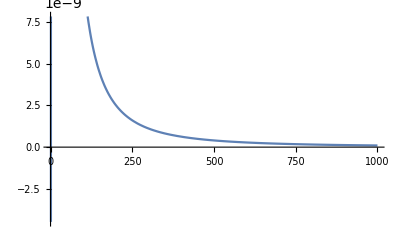

```mathematica
Plot[y,{x,0,1000}]
```

```mathematica
chidata =Import["chi.txt", "CSV"]
```

{{1,197},{2,367},{3,464},{4,862},{5,1255},{6,1371},{7,1274},{8,1176},{9,1037},{10,858},{11,402},{12,236},{13,195},{14,113},{15,37},{16,4},{17,3},{18,0},{19,0},{20,0},{21,0},{22,0},{23,0},{24,0},{25,0},{26,0},{27,0},{28,0},{29,0},{30,0},{31,0},{32,0},{33,0},{34,0},{35,0},{36,0},{37,0},{38,0},{39,0},{40,0},{41,0},{42,0},{43,0},{44,0},{45,0},{46,0},{47,0},{48,0},{49,0},{50,0},{51,0},{52,0},{53,0},{54,0},{55,0},{56,0},{57,0},{58,0},{59,0},{60,0},{61,0},{62,0},{63,0},{64,0},{65,0},{66,0},{67,0},{68,0},{69,0},{70,0},{71,0},{72,0},{73,0},{74,0},{75,0},{76,0},{77,0},{78,0},9695,{9774,0},{9775,0},{9776,0},{9777,0},{9778,0},{9779,0},{9780,0},{9781,0},{9782,0},{9783,0},{9784,0},{9785,0},{9786,0},{9787,0},{9788,0},{9789,0},{9790,0},{9791,0},{9792,0},{9793,0},{9794,0},{9795,0},{9796,0},{9797,0},{9798,0},{9799,0},{9800,0},{9801,0},{9802,0},{9803,0},{9804,0},{9805,0},{9806,0},{9807,0},{9808,0},{9809,0},{9810,0},{9811,0},{9812,0},{9813,0},{9814,0},{9815,0},{9816,0},{9817,0},{9818,0},{9819,0},{9820,0},{9821,0},{9822,0},{9823,0},{9824,0},{9825,0},{9826,0},{9827,0},{9828,0},{9829,0},{9830,0},{9831,0},{9832,0},{9833,0},{9834,0},{9835,0},{9836,0},{9837,0},{9838,0},{9839,0},{9840,0},{9841,0},{9842,0},{9843,0},{9844,0},{9845,0},{9846,0},{9847,0},{9848,0},{9849,0},{9850,0}}
 |  |  |  |

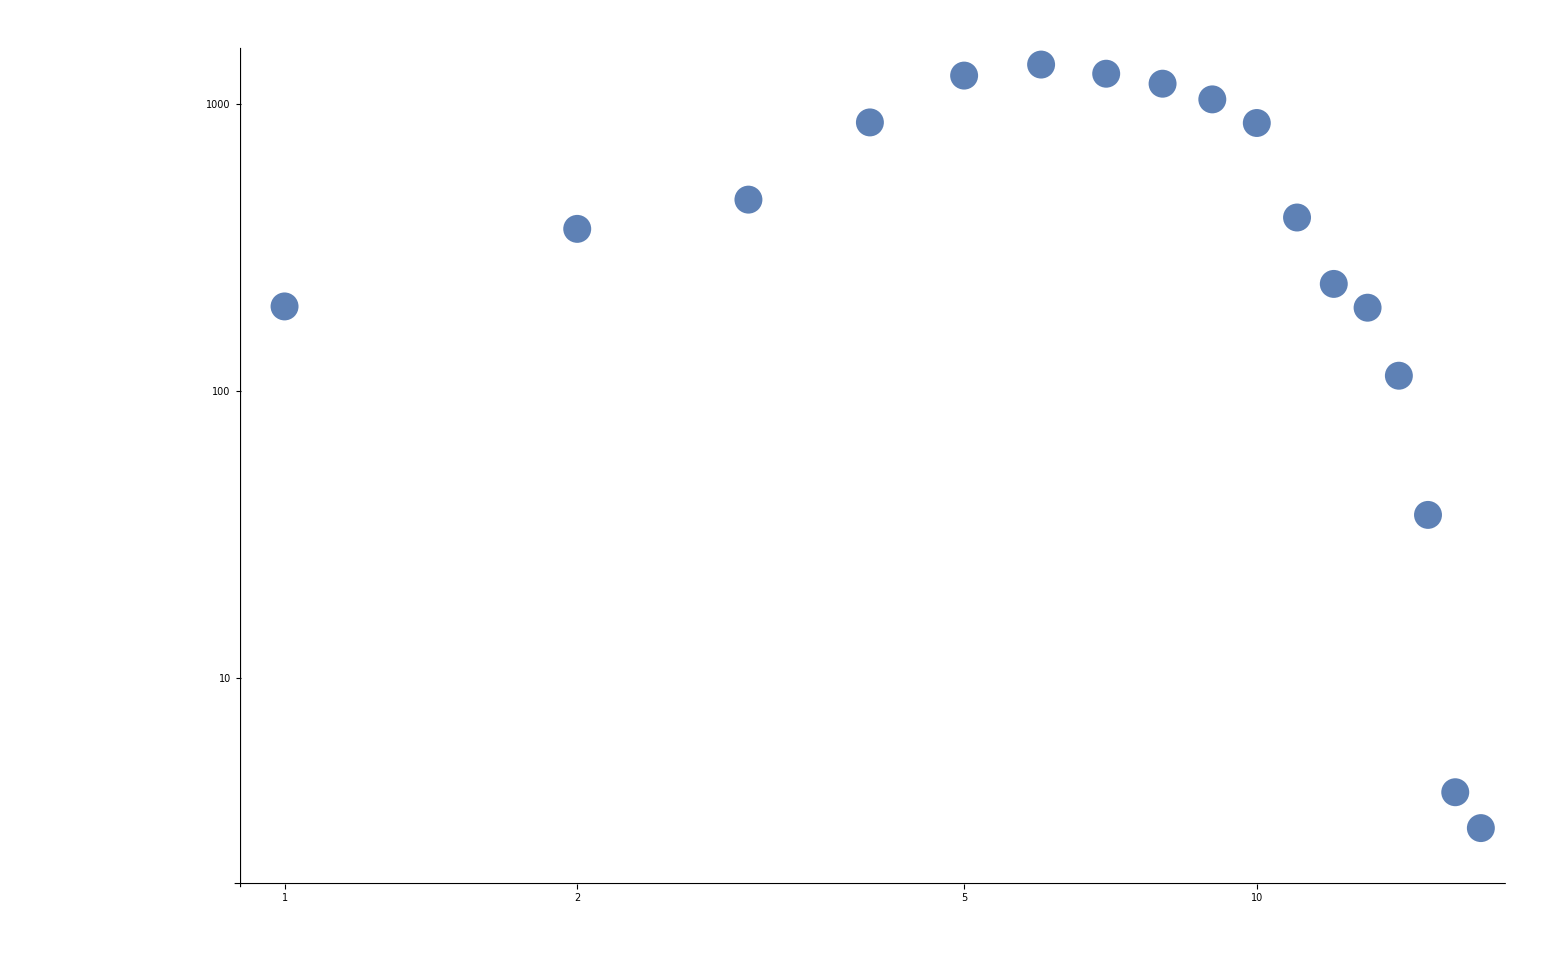

```mathematica
ListLogLogPlot[{chidata},PlotRange->All]
```

```mathematica
datanew=Import["array.txt", "CSV"]
```

{1}
 |  |  |  |

```mathematica
ArrayPlot[datanew, ColorFunction->"Rainbow"]
```

-Graphics-

```mathematica
chinewdata = Import["chinew.txt", "CSV"]
```

{{0,1},{1,3158},{2,1314},{3,652},{4,454},{5,339},{6,273},{7,217},{8,171},{9,144},{10,124},{11,95},{12,115},{13,89},{14,66},{15,77},{16,71},{17,50},{18,56},{19,52},{20,47},{21,45},{22,45},{23,37},{24,24},{25,22},{26,38},{27,33},{28,33},{29,29},{30,19},{31,21},{32,25},{33,24},{34,21},{35,16},{36,16},{37,22},{38,19},{39,22},{40,27},{41,15},{42,16},{43,13},{44,11},{45,13},{46,17},{47,16},{48,16},{49,10},{50,7},{51,16},{52,14},{53,12},{54,16},{55,17},{56,8},{57,9},{58,13},{59,9},{60,9},{61,11},{62,5},{63,9},{64,11},{65,13},{66,9},{67,12},{68,15},{69,16},{70,11},{71,5},{72,5},{73,5},{74,9},9702,{9777,0},{9778,0},{9779,0},{9780,0},{9781,0},{9782,0},{9783,0},{9784,0},{9785,0},{9786,0},{9787,0},{9788,0},{9789,0},{9790,0},{9791,0},{9792,0},{9793,0},{9794,0},{9795,0},{9796,0},{9797,0},{9798,0},{9799,0},{9800,0},{9801,0},{9802,0},{9803,0},{9804,0},{9805,0},{9806,0},{9807,0},{9808,0},{9809,0},{9810,0},{9811,0},{9812,0},{9813,0},{9814,0},{9815,0},{9816,0},{9817,0},{9818,0},{9819,0},{9820,0},{9821,0},{9822,0},{9823,0},{9824,0},{9825,0},{9826,0},{9827,0},{9828,0},{9829,0},{9830,0},{9831,0},{9832,0},{9833,0},{9834,0},{9835,0},{9836,0},{9837,0},{9838,0},{9839,0},{9840,0},{9841,0},{9842,0},{9843,0},{9844,0},{9845,0},{9846,1},{9847,0},{9848,0},{9849,0},{9850,0},{9851,0}}
 |  |  |  |

```mathematica
dataacc=chinewdata;
dataacc[[All,2]]=9729-Accumulate[(chinewdata[[All,2]])]
```

{9728,6570,5256,4604,4150,3811,3538,3321,3150,3006,2882,2787,2672,2583,2517,2440,2369,2319,2263,2211,2164,2119,2074,2037,2013,1991,1953,1920,1887,1858,1839,1818,1793,1769,1748,1732,1716,1694,1675,1653,1626,1611,1595,1582,1571,1558,1541,1525,1509,1499,1492,1476,1462,1450,1434,1417,1409,1400,1387,1378,1369,1358,1353,1344,1333,1320,1311,1299,1284,1268,1257,1252,1247,1242,1233,1226,1222,1212,1205,1196,1187,1179,1173,1165,1154,1147,1144,1137,1129,1119,1109,1105,1099,1093,1086,1080,1075,1067,1062,1060,1052,1047,1044,1039,1029,1023,1020,1010,1007,1000,996,989,984,984,982,977,976,971,964,962,958,955,950,946,943,939,931,926,925,921,917,913,911,908,906,900,898,897,893,888,886,884,881,880,873,870,864,858,856,853,850,847,845,845,843,842,839,834,830,826,824,821,819,815,813,810,808,807,805,800,797,795,794,790,788,788,786,785,784,781,779,778,776,774,774,772,771,771,766,763,762,756,756,752,750,748,746,744,742,741,740,736,734,731,728,726,724,722,722,719,718,717,717,717,714,711,709,708,706,705,702,700,696,695,695,694,693,690,686,686,684,679,677,676,675,672,671,668,668,668,668,668,665,664,660,658,657,656,655,653,650,647,647,645,645,644,642,640,640,640,638,638,636,634,633,633,632,630,630,627,626,626,624,624,621,619,618,618,616,615,614,613,612,611,610,609,608,607,606,606,606,604,604,601,600,597,596,595,594,593,593,592,592,591,589,587,587,587,585,585,585,585,585,584,583,582,580,578,578,578,576,575,574,574,573,572,571,567,567,565,563,562,561,560,560,559,557,557,557,556,556,554,553,553,551,551,549,549,548,545,545,545,543,543,543,542,540,539,538,537,537,535,534,534,532,531,531,531,531,530,530,528,528,527,526,524,524,524,524,524,523,523,523,523,523,523,521,520,520,520,520,518,517,516,516,516,516,516,515,514,514,514,513,512,511,511,509,508,507,507,505,504,504,503,503,502,501,501,501,501,500,499,499,499,497,497,497,497,495,495,494,494,493,490,488,488,487,487,487,487,484,483,483,482,482,480,478,478,476,474,473,471,470,470,470,470,469,468,468,468,467,463,460,457,454,454,454,454,453,453,452,452,452,452,450,448,448,448,448,448,446,445,445,445,445,444,444,444,442,441,441,441,441,440,439,439,439,438,438,438,437,436,435,435,434,434,434,433,432,432,431,431,431,431,431,431,431,431,430,429,429,429,427,427,427,427,427,426,426,425,425,424,424,424,423,422,422,421,421,420,420,420,419,419,419,419,419,419,418,418,417,416,416,416,416,415,415,414,414,413,413,412,412,412,411,411,410,410,410,410,409,409,409,407,406,406,405,405,405,405,405,405,405,405,404,403,403,403,403,402,402,402,402,402,401,401,401,401,401,401,401,400,400,400,398,398,398,397,397,397,397,397,395,395,394,394,394,394,392,392,392,392,392,392,392,392,392,392,390,389,389,389,389,389,388,387,387,385,385,385,385,385,385,383,382,382,382,382,382,382,382,382,381,381,381,381,381,381,381,381,380,379,378,378,378,377,375,375,375,375,375,375,375,375,375,375,375,373,372,371,371,371,370,370,370,370,369,369,369,369,369,369,369,368,367,367,367,367,366,365,364,363,362,362,362,362,361,361,361,360,360,360,360,360,359,357,357,357,356,356,356,356,355,354,354,354,354,354,354,354,354,354,354,354,354,354,354,353,353,353,353,353,353,353,353,353,352,352,352,352,352,352,352,352,352,352,352,352,352,351,351,351,351,350,349,349,349,349,347,346,345,345,344,343,343,343,343,343,342,342,342,340,339,339,338,338,338,337,337,337,337,337,337,337,337,336,335,335,335,335,335,335,335,335,335,334,334,334,333,333,332,331,329,329,329,329,329,329,329,329,329,329,329,329,328,328,328,328,328,328,328,328,328,328,328,328,327,327,327,327,326,326,326,325,325,325,325,324,324,323,323,321,321,320,320,320,320,319,319,319,319,319,319,319,319,319,318,318,318,318,317,316,316,316,316,316,316,316,316,316,316,316,316,316,316,316,316,315,315,315,315,315,315,314,314,314,314,314,314,314,314,314,314,314,314,314,313,313,313,312,311,311,311,310,310,309,308,308,308,308,307,307,307,307,307,307,307,307,307,307,307,307,307,307,307,307,307,306,306,306,305,305,305,305,305,305,305,305,305,304,304,304,303,303,303,303,303,303,303,302,302,301,301,301,301,301,301,301,301,301,301,300,300,299,299,298,298,297,297,297,296,296,296,296,296,296,296,296,296,295,295,295,295,295,294,294,293,293,293,293,293,293,293,293,292,292,292,292,291,291,289,289,289,289,288,287,287,287,287,286,285,285,285,285,285,285,285,285,284,283,283,282,282,281,281,281,280,280,280,280,280,279,279,279,279,279,279,279,279,279,279,277,277,276,275,275,275,275,275,274,273,272,272,272,272,272,272,271,271,271,270,270,270,270,270,269,269,269,269,269,269,269,269,268,268,268,268,268,268,268,268,268,268,268,268,268,268,268,268,268,268,268,268,268,268,268,268,268,268,268,268,268,268,268,268,268,268,268,268,268,267,267,267,266,266,266,266,266,265,265,265,265,265,265,265,265,265,264,263,263,263,263,263,263,263,263,263,263,263,263,263,261,261,260,260,260,259,259,259,259,259,258,257,257,257,255,255,255,255,255,254,254,254,254,254,254,254,254,254,254,254,253,252,252,251,251,250,250,249,249,249,249,249,249,249,249,249,249,248,248,247,247,247,247,247,247,247,247,247,247,247,247,247,247,247,247,247,247,247,247,247,246,246,246,246,246,246,246,246,246,246,246,246,246,246,246,246,246,246,246,246,246,246,246,246,246,246,246,246,246,246,245,245,245,245,245,245,245,245,245,245,245,245,245,245,245,245,245,245,245,245,245,245,245,245,244,244,244,244,244,244,244,244,243,243,243,243,243,243,243,243,243,243,243,243,243,243,243,243,243,243,243,243,243,243,243,243,243,243,243,243,242,242,242,242,242,242,242,242,242,242,242,242,242,242,242,242,242,242,242,242,242,242,242,241,241,241,241,241,241,241,241,241,241,241,241,241,241,241,241,241,241,241,241,241,241,240,240,240,240,240,240,240,239,238,238,238,238,238,237,237,237,237,237,237,237,237,237,237,237,237,237,237,237,237,237,237,237,237,236,235,235,235,234,234,234,234,234,234,234,234,234,234,234,234,234,234,234,234,233,233,233,233,233,233,233,233,233,233,232,232,232,232,232,232,232,232,232,232,232,232,232,232,232,232,232,231,230,230,230,230,230,230,230,230,229,229,229,229,229,229,229,229,229,229,229,229,229,229,229,229,229,228,228,228,228,228,228,228,228,228,227,227,227,227,227,227,227,227,227,227,227,226,226,226,226,226,226,225,225,225,225,224,224,224,224,224,224,224,224,224,224,224,223,223,223,223,223,222,222,222,222,222,222,222,222,222,222,222,222,222,221,221,221,221,221,221,221,221,221,221,221,220,220,220,220,220,220,220,220,220,220,220,219,219,219,219,219,219,218,218,218,218,218,218,216,216,216,216,216,216,216,216,216,216,216,216,216,216,216,216,216,216,216,216,216,216,215,215,215,215,215,215,215,215,215,215,215,215,215,215,215,215,215,215,214,214,214,214,213,213,213,212,212,212,212,212,212,211,211,211,211,211,211,211,211,211,211,211,211,211,211,211,211,211,211,211,211,211,211,211,211,211,211,211,211,211,211,211,211,211,211,211,211,211,211,211,210,210,210,210,210,210,210,210,210,210,210,209,209,209,209,209,209,209,209,209,209,209,209,209,209,209,209,209,209,209,209,209,209,209,209,209,209,209,209,209,209,209,209,209,209,209,209,209,209,209,209,209,209,209,209,209,209,209,209,209,209,209,209,209,209,209,209,209,209,209,209,209,209,209,209,209,209,209,209,209,209,209,209,209,209,209,209,209,209,209,209,209,209,209,209,209,208,208,208,208,208,208,208,208,208,208,208,208,208,208,208,208,208,208,208,208,208,207,207,207,207,207,207,207,207,207,207,207,207,207,207,207,207,207,207,206,205,205,205,205,205,204,204,204,204,204,204,204,204,203,202,202,202,202,202,201,201,201,201,201,201,201,201,200,200,200,199,199,199,199,199,199,198,198,198,198,198,198,198,198,198,198,198,198,198,198,198,197,197,197,197,197,197,197,197,197,197,197,197,197,197,197,197,197,197,197,197,197,197,197,197,197,197,197,197,197,197,197,197,196,196,196,196,196,196,196,196,196,196,196,196,196,196,196,196,196,196,196,196,196,196,196,196,196,196,196,196,196,196,196,196,196,195,195,195,195,195,195,195,195,194,194,194,194,194,194,194,194,194,194,194,194,194,194,194,194,193,193,193,193,193,193,193,193,193,193,193,193,193,193,193,193,193,193,193,193,193,193,193,193,193,192,191,191,191,191,191,191,191,191,191,191,191,191,191,190,190,190,190,190,190,190,190,190,190,190,190,190,190,190,190,190,190,190,190,190,190,190,190,190,190,189,188,188,188,188,188,188,188,188,188,188,188,188,188,188,188,188,188,188,188,188,188,188,188,188,188,188,188,188,188,188,188,188,188,188,188,188,188,188,188,188,188,187,187,187,187,187,186,186,186,186,186,186,186,185,185,185,185,185,185,185,185,185,185,185,185,184,184,184,184,184,184,184,184,184,184,184,184,184,184,184,184,184,184,184,184,184,184,184,184,184,184,184,183,182,182,182,182,182,182,181,181,181,181,181,181,181,181,181,181,181,181,181,181,181,181,181,181,181,181,181,181,181,181,181,181,181,181,181,181,181,181,181,181,180,180,180,180,180,180,180,180,180,180,180,180,180,180,180,180,180,180,180,180,180,180,180,180,180,180,180,180,180,180,180,180,180,180,180,180,179,179,179,179,179,179,178,178,178,178,178,178,178,178,178,178,178,178,178,178,177,177,177,176,175,175,175,175,175,175,175,175,175,175,175,175,174,174,174,174,174,174,174,174,174,174,174,173,173,173,173,173,173,173,173,173,173,172,172,172,172,172,172,172,172,172,172,172,172,172,172,172,171,171,171,171,171,171,171,171,171,171,171,171,171,171,171,171,171,171,171,171,171,171,171,171,171,171,171,170,170,170,170,169,168,168,168,168,168,168,168,168,168,168,168,168,168,167,166,166,166,166,166,166,166,166,166,166,166,166,166,166,166,166,166,166,166,166,166,166,166,166,165,165,165,165,165,165,165,164,164,164,164,164,164,164,164,164,164,164,163,163,163,163,163,163,163,163,163,163,163,163,163,162,162,162,162,162,162,162,162,162,162,162,162,162,161,161,161,161,161,161,161,161,161,161,160,159,159,157,157,157,157,157,157,157,157,157,157,157,157,157,157,157,157,157,157,157,157,157,157,157,157,157,157,157,157,157,157,157,157,157,156,156,156,156,156,156,156,156,156,156,156,156,155,155,155,155,155,155,155,155,155,155,155,155,155,155,155,155,155,155,155,155,155,155,155,155,155,155,155,155,154,154,154,154,154,154,154,154,153,153,153,153,153,153,153,153,153,153,153,153,153,153,153,153,153,153,153,153,153,153,153,153,153,153,153,153,153,153,153,153,153,153,153,153,153,153,153,153,153,153,153,153,153,153,153,153,153,153,153,153,153,153,153,153,153,153,153,153,153,153,153,153,153,153,153,153,153,153,152,152,152,152,151,151,151,151,151,151,151,151,151,151,151,151,151,151,151,151,151,151,150,150,150,150,150,150,150,150,150,150,150,150,150,150,150,150,150,150,150,150,150,150,150,150,150,150,150,150,150,150,150,150,150,150,149,149,149,149,149,148,147,147,147,147,147,147,147,147,147,147,147,147,147,147,147,147,147,147,147,147,147,147,147,147,147,147,147,147,147,147,147,147,147,147,147,147,147,147,147,147,147,147,147,147,147,147,147,147,147,147,147,147,147,147,147,147,147,147,147,147,147,146,146,146,146,146,146,146,146,146,146,146,146,146,146,146,146,146,146,146,146,146,146,146,146,146,146,146,146,146,146,146,146,146,146,146,146,146,146,145,145,145,144,144,144,144,144,144,144,144,144,144,144,144,144,144,144,144,144,144,144,144,144,144,144,144,144,144,144,144,144,144,144,144,144,144,144,143,143,143,143,143,143,143,143,143,143,143,143,143,143,143,143,143,143,143,143,143,143,143,143,143,143,143,143,143,143,143,143,143,143,143,143,143,143,143,143,143,143,143,143,142,142,142,142,142,142,142,142,142,142,142,142,142,142,142,142,142,142,142,142,142,142,142,142,142,142,142,142,142,141,141,141,141,141,141,141,141,141,141,141,141,141,141,140,140,140,140,140,140,140,140,139,139,139,139,139,139,139,139,139,139,139,139,139,139,139,139,138,138,138,138,138,138,138,138,138,138,138,138,138,138,138,138,138,138,138,138,138,138,138,138,138,138,137,136,136,136,136,136,135,135,135,135,135,135,135,135,135,135,135,135,135,135,135,135,135,135,135,135,135,135,135,135,135,135,135,134,134,134,134,133,133,133,133,133,133,133,133,133,133,133,133,133,133,133,133,133,133,133,133,133,133,133,133,133,133,133,133,133,133,133,133,133,133,133,133,133,133,133,133,133,133,133,133,133,133,133,133,133,133,133,133,133,133,133,133,133,133,133,133,133,133,133,133,133,133,133,133,133,133,133,133,133,133,133,133,133,133,131,131,131,131,131,131,131,131,131,131,131,131,131,131,131,131,131,131,131,131,131,131,131,131,131,131,131,131,131,131,131,131,131,131,131,131,131,131,131,131,131,131,131,131,131,131,131,131,131,131,131,131,131,131,131,131,131,131,130,130,130,130,130,130,130,130,130,130,129,129,129,129,129,129,129,129,129,129,129,129,129,129,128,128,128,128,128,128,128,128,127,127,127,127,127,127,127,127,127,127,127,127,127,127,127,127,127,127,127,127,127,127,127,127,127,127,127,127,127,126,126,126,126,126,126,126,126,126,126,126,126,126,126,126,126,126,126,126,126,126,126,126,126,126,126,126,126,126,126,126,125,125,125,125,125,125,125,125,125,125,125,125,125,125,125,125,125,125,124,124,124,124,124,124,124,124,124,123,123,123,123,123,123,123,123,123,123,123,123,123,123,123,123,122,122,122,122,122,122,122,122,122,122,122,122,122,122,122,122,122,122,121,121,121,121,121,121,120,120,120,120,120,120,120,120,120,120,120,120,120,120,120,120,120,120,120,120,120,120,120,120,120,120,120,120,120,120,120,120,120,120,120,120,119,119,119,119,119,119,119,119,119,119,119,119,119,119,118,118,118,118,118,118,118,118,118,118,118,118,118,118,118,118,118,118,118,118,117,117,117,116,116,116,116,116,116,116,116,116,116,116,116,116,116,116,116,116,116,116,116,116,116,116,116,116,116,116,116,116,116,116,116,116,116,116,115,115,115,115,115,115,115,115,115,115,115,115,115,115,115,115,115,115,115,114,114,114,114,114,114,114,114,114,114,114,114,113,113,113,113,113,113,113,113,113,113,113,113,113,113,113,113,113,113,113,113,113,113,113,113,113,113,113,113,113,113,113,113,113,113,113,113,113,113,113,113,113,113,113,112,112,112,112,112,112,112,111,111,111,111,111,111,111,111,111,111,111,111,111,111,111,111,111,111,111,111,111,111,111,110,110,109,109,109,109,108,108,108,107,107,107,107,107,107,106,106,106,106,106,106,106,106,106,106,106,106,106,106,106,106,106,106,105,105,105,105,105,105,105,104,104,104,104,104,104,104,104,104,104,104,104,104,103,103,103,103,103,103,103,103,103,103,103,103,103,103,103,103,103,103,103,103,103,103,103,102,102,102,102,102,102,102,102,102,102,102,102,102,102,102,102,102,102,102,102,102,102,102,102,101,101,101,101,101,101,101,101,101,101,101,101,101,101,101,100,100,100,100,100,100,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,98,98,98,98,98,98,98,98,98,98,98,98,98,98,98,98,98,98,98,98,98,98,98,98,98,98,98,98,98,98,98,98,98,98,98,98,98,97,97,97,97,97,97,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,95,95,95,95,95,95,95,95,95,95,95,95,95,95,95,95,95,95,95,95,95,95,95,95,95,95,95,95,95,95,95,95,95,95,95,95,95,95,95,95,95,95,95,95,95,95,95,95,95,95,95,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,93,93,93,93,93,93,93,93,93,93,93,93,93,93,93,93,93,93,93,93,93,93,93,93,93,93,93,93,93,93,93,93,93,93,93,93,93,93,93,93,93,93,93,93,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,91,91,91,91,91,91,91,91,91,91,91,91,91,91,91,91,91,91,91,91,91,91,91,91,91,91,91,90,90,90,90,90,90,90,90,90,90,90,90,90,90,90,90,90,90,90,90,90,90,90,90,90,90,90,90,90,90,90,90,90,90,90,90,89,89,89,89,89,89,89,89,89,89,89,89,89,89,89,89,89,89,89,89,89,89,89,89,89,89,89,89,89,88,87,87,87,87,87,87,87,87,87,87,86,86,86,86,86,86,86,86,86,86,86,86,86,86,86,86,86,86,86,86,86,86,86,86,86,86,86,86,86,86,86,86,86,86,86,86,86,86,86,86,86,86,86,86,86,86,86,86,86,86,86,86,86,86,86,86,86,86,86,86,86,86,86,86,86,86,86,86,86,86,86,86,86,86,86,86,86,86,86,86,86,86,86,86,86,86,86,85,85,85,85,85,85,85,85,85,85,85,85,85,85,85,85,85,85,85,85,85,85,85,85,85,85,85,85,85,85,85,85,85,85,85,85,85,85,85,85,85,85,85,85,85,85,85,85,85,85,85,85,85,85,85,85,85,85,85,85,85,85,85,85,85,85,85,85,85,85,85,85,85,85,85,85,85,85,85,85,85,85,85,85,85,85,85,84,84,84,84,84,84,84,84,84,84,84,84,84,84,84,84,84,84,84,84,84,84,84,84,84,84,84,84,84,84,84,84,83,83,83,83,83,83,83,83,83,83,83,83,83,83,83,83,83,83,83,83,83,83,83,83,83,83,83,83,83,83,82,81,81,81,81,81,81,81,81,81,81,81,81,81,81,81,81,81,81,81,81,81,81,81,81,81,81,81,81,81,81,81,81,81,81,81,81,81,81,81,81,81,80,80,80,80,80,79,79,79,79,79,79,79,79,78,78,78,78,78,78,78,78,78,78,78,78,78,78,78,78,78,78,78,78,78,78,78,78,78,78,78,78,78,78,78,78,78,78,78,78,78,78,78,78,78,78,78,78,78,78,78,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,76,76,76,76,76,76,76,76,76,76,76,76,76,76,76,76,76,76,76,76,76,76,75,75,75,75,75,74,74,74,74,74,74,74,74,74,74,74,74,74,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,71,71,71,71,71,71,71,71,71,71,71,71,71,71,71,71,71,71,71,70,70,70,70,70,70,70,70,70,69,69,69,69,69,68,68,68,68,68,68,68,68,68,68,68,68,68,68,68,68,68,68,68,68,68,68,68,68,68,68,68,68,68,66,66,66,66,66,66,66,66,66,66,66,66,66,66,66,66,66,66,66,66,66,66,66,66,66,66,66,66,66,66,66,66,66,66,66,66,66,66,66,66,66,66,66,66,66,66,66,66,66,66,66,66,66,66,66,66,66,66,66,66,66,66,66,66,66,66,66,66,66,66,66,66,66,66,66,66,66,66,66,66,66,66,66,66,66,66,66,66,66,66,66,66,66,66,66,66,66,66,66,66,66,66,66,65,65,65,65,65,65,65,65,65,65,65,65,65,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,62,62,62,62,62,62,62,62,62,62,62,62,62,62,62,62,62,62,62,62,62,62,62,62,62,62,62,62,62,62,62,62,62,62,62,62,62,62,62,62,62,62,62,62,62,62,62,62,62,62,62,62,62,62,62,62,62,62,62,62,62,62,62,62,62,62,62,62,62,62,62,62,62,62,62,62,62,62,62,62,62,62,62,62,62,62,62,62,62,62,62,62,62,62,62,61,61,61,61,61,61,61,61,61,61,61,61,61,61,61,61,61,61,61,61,61,61,61,61,61,61,61,61,61,61,61,61,61,61,61,61,61,61,61,61,61,61,61,61,61,61,61,61,61,61,61,61,61,61,61,61,61,61,61,61,61,61,61,61,61,61,61,61,61,61,61,61,61,61,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,59,59,59,59,59,59,59,59,59,59,59,59,59,59,59,59,59,59,59,59,59,59,59,59,59,59,59,59,59,59,59,59,59,59,59,59,59,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,53,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,50,50,50,50,49,49,49,49,49,49,49,49,49,49,49,49,49,49,49,49,49,49,49,49,49,49,49,49,49,49,49,49,49,49,49,49,49,49,49,49,49,49,49,49,49,49,49,49,49,49,49,49,49,48,48,48,48,48,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,45,45,45,45,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,43,43,43,43,43,43,43,43,43,43,43,43,43,43,43,43,43,43,43,43,43,43,43,43,43,43,43,43,43,43,43,43,43,43,43,43,43,42,42,42,42,42,42,42,42,42,42,42,42,42,42,42,42,42,41,41,41,41,41,41,41,41,41,41,41,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,30,30,30,30,30,30,30,30,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,27,27,27,27,27,27,27,27,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,25,25,25,25,25,25,25,25,25,25,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,22,22,22,22,22,22,22,22,22,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,20,20,20,20,20,20,20,20,20,20,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,5,5,5,5,5,5,5,5,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0}

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

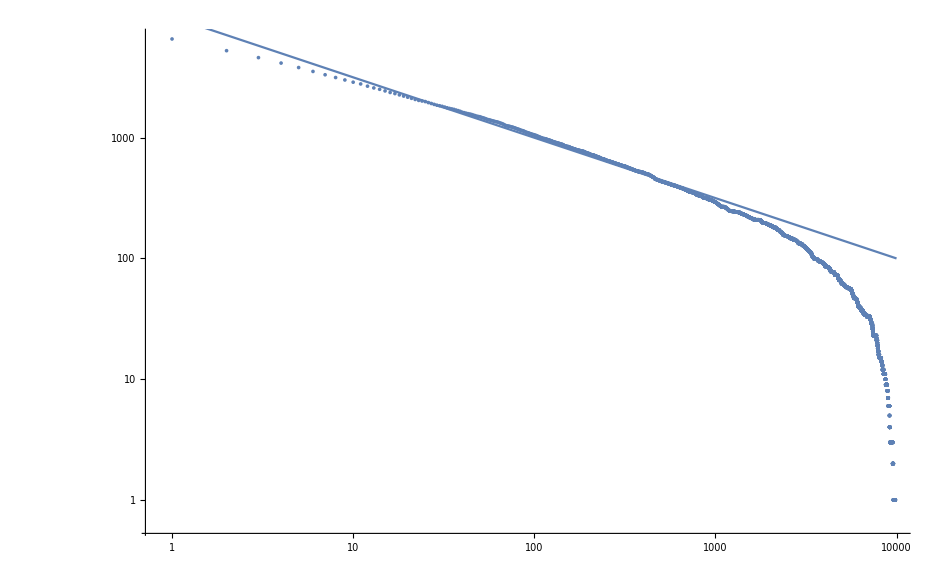

```mathematica
Show[ListLogLogPlot[{dataacc},PlotRange->All],LogLogPlot[10000/(x^0.5),{x,0.5,10000}]]
```

```mathematica
f = Import["fplot.txt" , "CSV"]
```

{{0,0},{1.17775×10^-6,7},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.0095×10^-6,6},{0.0231816,137781},{5.72049×10^-6,34},{1.6825×10^-7,1},{0.0148819,88451},{0.000342388,2035},{0.00897663,53353},{1.6825×10^-7,1},{5.04749×10^-7,3},{6.72999×10^-7,4},{0.0274045,162880},{1.6825×10^-7,1},{0.000014133,84},{0.00849324,50480},{3.70149×10^-6,22},{5.04749×10^-7,3},{1.6825×10^-7,1},{3.36499×10^-7,2},{1.6825×10^-7,1},{3.36499×10^-7,2},{1.0095×10^-6,6},{0.0181451,107846},{1.6825×10^-7,1},{0.0000124505,74},{0.0000370149,220},{1.6825×10^-7,1},{5.04749×10^-7,3},{1.6825×10^-7,1},{6.72999×10^-7,4},{0.0000307897,183},{0.0000139647,83},{2.019×10^-6,12},{1.6825×10^-7,1},9777,{1.6825×10^-7,1},{3.36499×10^-7,2},{3.36499×10^-7,2},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{3.36499×10^-7,2},{1.6825×10^-7,1},{5.04749×10^-7,3},{5.04749×10^-7,3},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{3.36499×10^-7,2},{3.36499×10^-7,2},{1.6825×10^-7,1},{3.36499×10^-7,2},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{3.36499×10^-7,2},{3.36499×10^-7,2},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{3.36499×10^-7,2},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1}}
 |  |  |  |

```mathematica
fsort = f
```

{{0,0},{1.17775×10^-6,7},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.0095×10^-6,6},{0.0231816,137781},{5.72049×10^-6,34},{1.6825×10^-7,1},{0.0148819,88451},{0.000342388,2035},{0.00897663,53353},{1.6825×10^-7,1},{5.04749×10^-7,3},{6.72999×10^-7,4},{0.0274045,162880},{1.6825×10^-7,1},{0.000014133,84},{0.00849324,50480},{3.70149×10^-6,22},{5.04749×10^-7,3},{1.6825×10^-7,1},{3.36499×10^-7,2},{1.6825×10^-7,1},{3.36499×10^-7,2},{1.0095×10^-6,6},{0.0181451,107846},{1.6825×10^-7,1},{0.0000124505,74},{0.0000370149,220},{1.6825×10^-7,1},{5.04749×10^-7,3},{1.6825×10^-7,1},{6.72999×10^-7,4},{0.0000307897,183},{0.0000139647,83},{2.019×10^-6,12},{1.6825×10^-7,1},9777,{1.6825×10^-7,1},{3.36499×10^-7,2},{3.36499×10^-7,2},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{3.36499×10^-7,2},{1.6825×10^-7,1},{5.04749×10^-7,3},{5.04749×10^-7,3},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{3.36499×10^-7,2},{3.36499×10^-7,2},{1.6825×10^-7,1},{3.36499×10^-7,2},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{3.36499×10^-7,2},{3.36499×10^-7,2},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{3.36499×10^-7,2},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1}}
 |  |  |  |

```mathematica
fsort[[1,All]]=SortBy[f,First]
```

{{0,0},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},9780,{0.00716289,42573},{0.00730187,43399},{0.0075137,44658},{0.00760472,45199},{0.00761212,45243},{0.00770769,45811},{0.00777297,46199},{0.00779013,46301},{0.0083472,49612},{0.00849324,50480},{0.0086376,51338},{0.00897663,53353},{0.00940196,55881},{0.0103314,61405},{0.0103455,61489},{0.0103472,61499},{0.0104624,62184},{0.0105018,62418},{0.0105392,62640},{0.0105501,62705},{0.0120203,71443},{0.013147,78140},{0.0134327,79838},{0.0148819,88451},{0.0149128,88635},{0.0150567,89490},{0.0180495,107278},{0.0181451,107846},{0.0192569,114454},{0.0194468,115583},{0.0210453,125084},{0.0223394,132775},{0.0227087,134970},{0.0231816,137781},{0.0272842,162165},{0.0274045,162880}}
 |  |  |  |

{{{0,0},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},9781,{0.00730187,43399},{0.0075137,44658},{0.00760472,45199},{0.00761212,45243},{0.00770769,45811},{0.00777297,46199},{0.00779013,46301},{0.0083472,49612},{0.00849324,50480},{0.0086376,51338},{0.00897663,53353},{0.00940196,55881},{0.0103314,61405},{0.0103455,61489},{0.0103472,61499},{0.0104624,62184},{0.0105018,62418},{0.0105392,62640},{0.0105501,62705},{0.0120203,71443},{0.013147,78140},{0.0134327,79838},{0.0148819,88451},{0.0149128,88635},{0.0150567,89490},{0.0180495,107278},{0.0181451,107846},{0.0192569,114454},{0.0194468,115583},{0.0210453,125084},{0.0223394,132775},{0.0227087,134970},{0.0231816,137781},{0.0272842,162165},{0.0274045,162880}},{1}}
 |  |  |  |

```mathematica
facc=fsort;
facc[[1,All]]=Accumulate[(fsort[[1,All]])]
```

{{{0,0},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{1.6825×10^-7,1},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{3.36499×10^-7,2},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{5.04749×10^-7,3},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{6.72999×10^-7,4},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{8.41249×10^-7,5},{1.0095×10^-6,6},{1.0095×10^-6,6},{1.0095×10^-6,6},{1.0095×10^-6,6},{1.0095×10^-6,6},{1.0095×10^-6,6},{1.0095×10^-6,6},{1.0095×10^-6,6},{1.0095×10^-6,6},{1.0095×10^-6,6},{1.0095×10^-6,6},{1.0095×10^-6,6},{1.0095×10^-6,6},{1.0095×10^-6,6},{1.0095×10^-6,6},{1.0095×10^-6,6},{1.0095×10^-6,6},{1.0095×10^-6,6},{1.0095×10^-6,6},{1.0095×10^-6,6},{1.0095×10^-6,6},{1.0095×10^-6,6},{1.0095×10^-6,6},{1.0095×10^-6,6},{1.0095×10^-6,6},{1.0095×10^-6,6},{1.0095×10^-6,6},{1.0095×10^-6,6},{1.0095×10^-6,6},{1.0095×10^-6,6},{1.0095×10^-6,6},{1.0095×10^-6,6},{1.0095×10^-6,6},{1.0095×10^-6,6},{1.0095×10^-6,6},{1.0095×10^-6,6},{1.0095×10^-6,6},{1.0095×10^-6,6},{1.0095×10^-6,6},{1.0095×10^-6,6},{1.0095×10^-6,6},{1.0095×10^-6,6},{1.0095×10^-6,6},{1.0095×10^-6,6},{1.0095×10^-6,6},{1.0095×10^-6,6},{1.0095×10^-6,6},{1.0095×10^-6,6},{1.0095×10^-6,6},{1.0095×10^-6,6},{1.0095×10^-6,6},{1.0095×10^-6,6},{1.0095×10^-6,6},{1.0095×10^-6,6},{1.0095×10^-6,6},{1.0095×10^-6,6},{1.0095×10^-6,6},{1.0095×10^-6,6},{1.0095×10^-6,6},{1.0095×10^-6,6},{1.0095×10^-6,6},{1.0095×10^-6,6},{1.0095×10^-6,6},{1.0095×10^-6,6},{1.0095×10^-6,6},{1.0095×10^-6,6},{1.0095×10^-6,6},{1.0095×10^-6,6},{1.0095×10^-6,6},{1.0095×10^-6,6},{1.0095×10^-6,6},{1.0095×10^-6,6},{1.0095×10^-6,6},{1.0095×10^-6,6},{1.0095×10^-6,6},{1.0095×10^-6,6},{1.0095×10^-6,6},{1.0095×10^-6,6},{1.0095×10^-6,6},{1.0095×10^-6,6},{1.0095×10^-6,6},{1.0095×10^-6,6},{1.0095×10^-6,6},{1.0095×10^-6,6},{1.0095×10^-6,6},{1.0095×10^-6,6},{1.0095×10^-6,6},{1.0095×10^-6,6},{1.0095×10^-6,6},{1.0095×10^-6,6},{1.0095×10^-6,6},{1.0095×10^-6,6},{1.0095×10^-6,6},{1.0095×10^-6,6},{1.0095×10^-6,6},{1.0095×10^-6,6},{1.0095×10^-6,6},{1.0095×10^-6,6},{1.0095×10^-6,6},{1.0095×10^-6,6},{1.0095×10^-6,6},{1.0095×10^-6,6},{1.0095×10^-6,6},{1.0095×10^-6,6},{1.0095×10^-6,6},{1.0095×10^-6,6},{1.0095×10^-6,6},{1.0095×10^-6,6},{1.0095×10^-6,6},{1.0095×10^-6,6},{1.0095×10^-6,6},{1.0095×10^-6,6},{1.0095×10^-6,6},{1.0095×10^-6,6},{1.0095×10^-6,6},{1.0095×10^-6,6},{1.0095×10^-6,6},{1.0095×10^-6,6},{1.0095×10^-6,6},{1.0095×10^-6,6},{1.0095×10^-6,6},{1.0095×10^-6,6},{1.0095×10^-6,6},{1.0095×10^-6,6},{1.0095×10^-6,6},{1.0095×10^-6,6},{1.0095×10^-6,6},{1.0095×10^-6,6},{1.0095×10^-6,6},{1.0095×10^-6,6},{1.0095×10^-6,6},{1.0095×10^-6,6},{1.0095×10^-6,6},{1.0095×10^-6,6},{1.0095×10^-6,6},{1.0095×10^-6,6},{1.0095×10^-6,6},{1.0095×10^-6,6},{1.0095×10^-6,6},{1.0095×10^-6,6},{1.0095×10^-6,6},{1.0095×10^-6,6},{1.0095×10^-6,6},{1.0095×10^-6,6},{1.0095×10^-6,6},{1.0095×10^-6,6},{1.0095×10^-6,6},{1.0095×10^-6,6},{1.0095×10^-6,6},{1.0095×10^-6,6},{1.0095×10^-6,6},{1.0095×10^-6,6},{1.0095×10^-6,6},{1.0095×10^-6,6},{1.0095×10^-6,6},{1.0095×10^-6,6},{1.0095×10^-6,6},{1.0095×10^-6,6},{1.0095×10^-6,6},{1.0095×10^-6,6},{1.0095×10^-6,6},{1.0095×10^-6,6},{1.0095×10^-6,6},{1.0095×10^-6,6},{1.0095×10^-6,6},{1.0095×10^-6,6},{1.0095×10^-6,6},{1.0095×10^-6,6},{1.0095×10^-6,6},{1.0095×10^-6,6},{1.0095×10^-6,6},{1.0095×10^-6,6},{1.0095×10^-6,6},{1.0095×10^-6,6},{1.0095×10^-6,6},{1.0095×10^-6,6},{1.0095×10^-6,6},{1.0095×10^-6,6},{1.0095×10^-6,6},{1.0095×10^-6,6},{1.0095×10^-6,6},{1.0095×10^-6,6},{1.0095×10^-6,6},{1.0095×10^-6,6},{1.0095×10^-6,6},{1.0095×10^-6,6},{1.0095×10^-6,6},{1.0095×10^-6,6},{1.0095×10^-6,6},{1.0095×10^-6,6},{1.0095×10^-6,6},{1.0095×10^-6,6},{1.0095×10^-6,6},{1.0095×10^-6,6},{1.0095×10^-6,6},{1.0095×10^-6,6},{1.0095×10^-6,6},{1.0095×10^-6,6},{1.0095×10^-6,6},{1.0095×10^-6,6},{1.0095×10^-6,6},{1.0095×10^-6,6},{1.0095×10^-6,6},{1.0095×10^-6,6},{1.0095×10^-6,6},{1.0095×10^-6,6},{1.0095×10^-6,6},{1.0095×10^-6,6},{1.0095×10^-6,6},{1.0095×10^-6,6},{1.0095×10^-6,6},{1.0095×10^-6,6},{1.0095×10^-6,6},{1.0095×10^-6,6},{1.0095×10^-6,6},{1.0095×10^-6,6},{1.0095×10^-6,6},{1.0095×10^-6,6},{1.0095×10^-6,6},{1.0095×10^-6,6},{1.0095×10^-6,6},{1.0095×10^-6,6},{1.0095×10^-6,6},{1.0095×10^-6,6},{1.0095×10^-6,6},{1.0095×10^-6,6},{1.0095×10^-6,6},{1.0095×10^-6,6},{1.0095×10^-6,6},{1.0095×10^-6,6},{1.0095×10^-6,6},{1.0095×10^-6,6},{1.0095×10^-6,6},{1.0095×10^-6,6},{1.0095×10^-6,6},{1.0095×10^-6,6},{1.0095×10^-6,6},{1.0095×10^-6,6},{1.0095×10^-6,6},{1.0095×10^-6,6},{1.0095×10^-6,6},{1.0095×10^-6,6},{1.0095×10^-6,6},{1.0095×10^-6,6},{1.0095×10^-6,6},{1.0095×10^-6,6},{1.0095×10^-6,6},{1.0095×10^-6,6},{1.0095×10^-6,6},{1.0095×10^-6,6},{1.0095×10^-6,6},{1.0095×10^-6,6},{1.0095×10^-6,6},{1.0095×10^-6,6},{1.0095×10^-6,6},{1.0095×10^-6,6},{1.0095×10^-6,6},{1.0095×10^-6,6},{1.0095×10^-6,6},{1.0095×10^-6,6},{1.0095×10^-6,6},{1.0095×10^-6,6},{1.0095×10^-6,6},{1.0095×10^-6,6},{1.0095×10^-6,6},{1.0095×10^-6,6},{1.0095×10^-6,6},{1.0095×10^-6,6},{1.0095×10^-6,6},{1.0095×10^-6,6},{1.0095×10^-6,6},{1.0095×10^-6,6},{1.0095×10^-6,6},{1.17775×10^-6,7},{1.17775×10^-6,7},{1.17775×10^-6,7},{1.17775×10^-6,7},{1.17775×10^-6,7},{1.17775×10^-6,7},{1.17775×10^-6,7},{1.17775×10^-6,7},{1.17775×10^-6,7},{1.17775×10^-6,7},{1.17775×10^-6,7},{1.17775×10^-6,7},{1.17775×10^-6,7},{1.17775×10^-6,7},{1.17775×10^-6,7},{1.17775×10^-6,7},{1.17775×10^-6,7},{1.17775×10^-6,7},{1.17775×10^-6,7},{1.17775×10^-6,7},{1.17775×10^-6,7},{1.17775×10^-6,7},{1.17775×10^-6,7},{1.17775×10^-6,7},{1.17775×10^-6,7},{1.17775×10^-6,7},{1.17775×10^-6,7},{1.17775×10^-6,7},{1.17775×10^-6,7},{1.17775×10^-6,7},{1.17775×10^-6,7},{1.17775×10^-6,7},{1.17775×10^-6,7},{1.17775×10^-6,7},{1.17775×10^-6,7},{1.17775×10^-6,7},{1.17775×10^-6,7},{1.17775×10^-6,7},{1.17775×10^-6,7},{1.17775×10^-6,7},{1.17775×10^-6,7},{1.17775×10^-6,7},{1.17775×10^-6,7},{1.17775×10^-6,7},{1.17775×10^-6,7},{1.17775×10^-6,7},{1.17775×10^-6,7},{1.17775×10^-6,7},{1.17775×10^-6,7},{1.17775×10^-6,7},{1.17775×10^-6,7},{1.17775×10^-6,7},{1.17775×10^-6,7},{1.17775×10^-6,7},{1.17775×10^-6,7},{1.17775×10^-6,7},{1.17775×10^-6,7},{1.17775×10^-6,7},{1.17775×10^-6,7},{1.17775×10^-6,7},{1.17775×10^-6,7},{1.17775×10^-6,7},{1.17775×10^-6,7},{1.17775×10^-6,7},{1.17775×10^-6,7},{1.17775×10^-6,7},{1.17775×10^-6,7},{1.17775×10^-6,7},{1.17775×10^-6,7},{1.17775×10^-6,7},{1.17775×10^-6,7},{1.17775×10^-6,7},{1.17775×10^-6,7},{1.17775×10^-6,7},{1.17775×10^-6,7},{1.17775×10^-6,7},{1.17775×10^-6,7},{1.17775×10^-6,7},{1.17775×10^-6,7},{1.17775×10^-6,7},{1.17775×10^-6,7},{1.17775×10^-6,7},{1.17775×10^-6,7},{1.17775×10^-6,7},{1.17775×10^-6,7},{1.17775×10^-6,7},{1.17775×10^-6,7},{1.17775×10^-6,7},{1.17775×10^-6,7},{1.17775×10^-6,7},{1.17775×10^-6,7},{1.17775×10^-6,7},{1.17775×10^-6,7},{1.17775×10^-6,7},{1.17775×10^-6,7},{1.17775×10^-6,7},{1.17775×10^-6,7},{1.17775×10^-6,7},{1.17775×10^-6,7},{1.17775×10^-6,7},{1.17775×10^-6,7},{1.17775×10^-6,7},{1.17775×10^-6,7},{1.17775×10^-6,7},{1.17775×10^-6,7},{1.17775×10^-6,7},{1.17775×10^-6,7},{1.17775×10^-6,7},{1.17775×10^-6,7},{1.17775×10^-6,7},{1.17775×10^-6,7},{1.17775×10^-6,7},{1.17775×10^-6,7},{1.17775×10^-6,7},{1.17775×10^-6,7},{1.17775×10^-6,7},{1.17775×10^-6,7},{1.17775×10^-6,7},{1.17775×10^-6,7},{1.17775×10^-6,7},{1.17775×10^-6,7},{1.17775×10^-6,7},{1.17775×10^-6,7},{1.17775×10^-6,7},{1.17775×10^-6,7},{1.17775×10^-6,7},{1.17775×10^-6,7},{1.17775×10^-6,7},{1.17775×10^-6,7},{1.17775×10^-6,7},{1.17775×10^-6,7},{1.17775×10^-6,7},{1.17775×10^-6,7},{1.17775×10^-6,7},{1.17775×10^-6,7},{1.17775×10^-6,7},{1.17775×10^-6,7},{1.17775×10^-6,7},{1.17775×10^-6,7},{1.17775×10^-6,7},{1.17775×10^-6,7},{1.17775×10^-6,7},{1.17775×10^-6,7},{1.17775×10^-6,7},{1.17775×10^-6,7},{1.17775×10^-6,7},{1.17775×10^-6,7},{1.17775×10^-6,7},{1.17775×10^-6,7},{1.17775×10^-6,7},{1.17775×10^-6,7},{1.17775×10^-6,7},{1.17775×10^-6,7},{1.17775×10^-6,7},{1.17775×10^-6,7},{1.17775×10^-6,7},{1.17775×10^-6,7},{1.17775×10^-6,7},{1.17775×10^-6,7},{1.17775×10^-6,7},{1.17775×10^-6,7},{1.17775×10^-6,7},{1.17775×10^-6,7},{1.17775×10^-6,7},{1.17775×10^-6,7},{1.17775×10^-6,7},{1.17775×10^-6,7},{1.17775×10^-6,7},{1.17775×10^-6,7},{1.17775×10^-6,7},{1.17775×10^-6,7},{1.17775×10^-6,7},{1.17775×10^-6,7},{1.17775×10^-6,7},{1.17775×10^-6,7},{1.17775×10^-6,7},{1.17775×10^-6,7},{1.17775×10^-6,7},{1.17775×10^-6,7},{1.17775×10^-6,7},{1.17775×10^-6,7},{1.17775×10^-6,7},{1.17775×10^-6,7},{1.17775×10^-6,7},{1.17775×10^-6,7},{1.17775×10^-6,7},{1.17775×10^-6,7},{1.17775×10^-6,7},{1.17775×10^-6,7},{1.17775×10^-6,7},{1.17775×10^-6,7},{1.17775×10^-6,7},{1.17775×10^-6,7},{1.17775×10^-6,7},{1.17775×10^-6,7},{1.17775×10^-6,7},{1.17775×10^-6,7},{1.17775×10^-6,7},{1.17775×10^-6,7},{1.17775×10^-6,7},{1.17775×10^-6,7},{1.17775×10^-6,7},{1.17775×10^-6,7},{1.17775×10^-6,7},{1.17775×10^-6,7},{1.17775×10^-6,7},{1.17775×10^-6,7},{1.17775×10^-6,7},{1.17775×10^-6,7},{1.17775×10^-6,7},{1.17775×10^-6,7},{1.17775×10^-6,7},{1.17775×10^-6,7},{1.17775×10^-6,7},{1.17775×10^-6,7},{1.17775×10^-6,7},{1.17775×10^-6,7},{1.346×10^-6,8},{1.346×10^-6,8},{1.346×10^-6,8},{1.346×10^-6,8},{1.346×10^-6,8},{1.346×10^-6,8},{1.346×10^-6,8},{1.346×10^-6,8},{1.346×10^-6,8},{1.346×10^-6,8},{1.346×10^-6,8},{1.346×10^-6,8},{1.346×10^-6,8},{1.346×10^-6,8},{1.346×10^-6,8},{1.346×10^-6,8},{1.346×10^-6,8},{1.346×10^-6,8},{1.346×10^-6,8},{1.346×10^-6,8},{1.346×10^-6,8},{1.346×10^-6,8},{1.346×10^-6,8},{1.346×10^-6,8},{1.346×10^-6,8},{1.346×10^-6,8},{1.346×10^-6,8},{1.346×10^-6,8},{1.346×10^-6,8},{1.346×10^-6,8},{1.346×10^-6,8},{1.346×10^-6,8},{1.346×10^-6,8},{1.346×10^-6,8},{1.346×10^-6,8},{1.346×10^-6,8},{1.346×10^-6,8},{1.346×10^-6,8},{1.346×10^-6,8},{1.346×10^-6,8},{1.346×10^-6,8},{1.346×10^-6,8},{1.346×10^-6,8},{1.346×10^-6,8},{1.346×10^-6,8},{1.346×10^-6,8},{1.346×10^-6,8},{1.346×10^-6,8},{1.346×10^-6,8},{1.346×10^-6,8},{1.346×10^-6,8},{1.346×10^-6,8},{1.346×10^-6,8},{1.346×10^-6,8},{1.346×10^-6,8},{1.346×10^-6,8},{1.346×10^-6,8},{1.346×10^-6,8},{1.346×10^-6,8},{1.346×10^-6,8},{1.346×10^-6,8},{1.346×10^-6,8},{1.346×10^-6,8},{1.346×10^-6,8},{1.346×10^-6,8},{1.346×10^-6,8},{1.346×10^-6,8},{1.346×10^-6,8},{1.346×10^-6,8},{1.346×10^-6,8},{1.346×10^-6,8},{1.346×10^-6,8},{1.346×10^-6,8},{1.346×10^-6,8},{1.346×10^-6,8},{1.346×10^-6,8},{1.346×10^-6,8},{1.346×10^-6,8},{1.346×10^-6,8},{1.346×10^-6,8},{1.346×10^-6,8},{1.346×10^-6,8},{1.346×10^-6,8},{1.346×10^-6,8},{1.346×10^-6,8},{1.346×10^-6,8},{1.346×10^-6,8},{1.346×10^-6,8},{1.346×10^-6,8},{1.346×10^-6,8},{1.346×10^-6,8},{1.346×10^-6,8},{1.346×10^-6,8},{1.346×10^-6,8},{1.346×10^-6,8},{1.346×10^-6,8},{1.346×10^-6,8},{1.346×10^-6,8},{1.346×10^-6,8},{1.346×10^-6,8},{1.346×10^-6,8},{1.346×10^-6,8},{1.346×10^-6,8},{1.346×10^-6,8},{1.346×10^-6,8},{1.346×10^-6,8},{1.346×10^-6,8},{1.346×10^-6,8},{1.346×10^-6,8},{1.346×10^-6,8},{1.346×10^-6,8},{1.346×10^-6,8},{1.346×10^-6,8},{1.346×10^-6,8},{1.346×10^-6,8},{1.346×10^-6,8},{1.346×10^-6,8},{1.346×10^-6,8},{1.346×10^-6,8},{1.346×10^-6,8},{1.346×10^-6,8},{1.346×10^-6,8},{1.346×10^-6,8},{1.346×10^-6,8},{1.346×10^-6,8},{1.346×10^-6,8},{1.346×10^-6,8},{1.346×10^-6,8},{1.346×10^-6,8},{1.346×10^-6,8},{1.346×10^-6,8},{1.346×10^-6,8},{1.346×10^-6,8},{1.346×10^-6,8},{1.346×10^-6,8},{1.346×10^-6,8},{1.346×10^-6,8},{1.346×10^-6,8},{1.346×10^-6,8},{1.346×10^-6,8},{1.346×10^-6,8},{1.346×10^-6,8},{1.346×10^-6,8},{1.346×10^-6,8},{1.346×10^-6,8},{1.346×10^-6,8},{1.346×10^-6,8},{1.346×10^-6,8},{1.346×10^-6,8},{1.346×10^-6,8},{1.346×10^-6,8},{1.346×10^-6,8},{1.346×10^-6,8},{1.346×10^-6,8},{1.346×10^-6,8},{1.346×10^-6,8},{1.346×10^-6,8},{1.346×10^-6,8},{1.346×10^-6,8},{1.346×10^-6,8},{1.346×10^-6,8},{1.346×10^-6,8},{1.346×10^-6,8},{1.346×10^-6,8},{1.346×10^-6,8},{1.346×10^-6,8},{1.346×10^-6,8},{1.346×10^-6,8},{1.346×10^-6,8},{1.346×10^-6,8},{1.346×10^-6,8},{1.51425×10^-6,9},{1.51425×10^-6,9},{1.51425×10^-6,9},{1.51425×10^-6,9},{1.51425×10^-6,9},{1.51425×10^-6,9},{1.51425×10^-6,9},{1.51425×10^-6,9},{1.51425×10^-6,9},{1.51425×10^-6,9},{1.51425×10^-6,9},{1.51425×10^-6,9},{1.51425×10^-6,9},{1.51425×10^-6,9},{1.51425×10^-6,9},{1.51425×10^-6,9},{1.51425×10^-6,9},{1.51425×10^-6,9},{1.51425×10^-6,9},{1.51425×10^-6,9},{1.51425×10^-6,9},{1.51425×10^-6,9},{1.51425×10^-6,9},{1.51425×10^-6,9},{1.51425×10^-6,9},{1.51425×10^-6,9},{1.51425×10^-6,9},{1.51425×10^-6,9},{1.51425×10^-6,9},{1.51425×10^-6,9},{1.51425×10^-6,9},{1.51425×10^-6,9},{1.51425×10^-6,9},{1.51425×10^-6,9},{1.51425×10^-6,9},{1.51425×10^-6,9},{1.51425×10^-6,9},{1.51425×10^-6,9},{1.51425×10^-6,9},{1.51425×10^-6,9},{1.51425×10^-6,9},{1.51425×10^-6,9},{1.51425×10^-6,9},{1.51425×10^-6,9},{1.51425×10^-6,9},{1.51425×10^-6,9},{1.51425×10^-6,9},{1.51425×10^-6,9},{1.51425×10^-6,9},{1.51425×10^-6,9},{1.51425×10^-6,9},{1.51425×10^-6,9},{1.51425×10^-6,9},{1.51425×10^-6,9},{1.51425×10^-6,9},{1.51425×10^-6,9},{1.51425×10^-6,9},{1.51425×10^-6,9},{1.51425×10^-6,9},{1.51425×10^-6,9},{1.51425×10^-6,9},{1.51425×10^-6,9},{1.51425×10^-6,9},{1.51425×10^-6,9},{1.51425×10^-6,9},{1.51425×10^-6,9},{1.51425×10^-6,9},{1.51425×10^-6,9},{1.51425×10^-6,9},{1.51425×10^-6,9},{1.51425×10^-6,9},{1.51425×10^-6,9},{1.51425×10^-6,9},{1.51425×10^-6,9},{1.51425×10^-6,9},{1.51425×10^-6,9},{1.51425×10^-6,9},{1.51425×10^-6,9},{1.51425×10^-6,9},{1.51425×10^-6,9},{1.51425×10^-6,9},{1.51425×10^-6,9},{1.51425×10^-6,9},{1.51425×10^-6,9},{1.51425×10^-6,9},{1.51425×10^-6,9},{1.51425×10^-6,9},{1.51425×10^-6,9},{1.51425×10^-6,9},{1.51425×10^-6,9},{1.51425×10^-6,9},{1.51425×10^-6,9},{1.51425×10^-6,9},{1.51425×10^-6,9},{1.51425×10^-6,9},{1.51425×10^-6,9},{1.51425×10^-6,9},{1.51425×10^-6,9},{1.51425×10^-6,9},{1.51425×10^-6,9},{1.51425×10^-6,9},{1.51425×10^-6,9},{1.51425×10^-6,9},{1.51425×10^-6,9},{1.51425×10^-6,9},{1.51425×10^-6,9},{1.51425×10^-6,9},{1.51425×10^-6,9},{1.51425×10^-6,9},{1.51425×10^-6,9},{1.51425×10^-6,9},{1.51425×10^-6,9},{1.51425×10^-6,9},{1.51425×10^-6,9},{1.51425×10^-6,9},{1.51425×10^-6,9},{1.51425×10^-6,9},{1.51425×10^-6,9},{1.51425×10^-6,9},{1.51425×10^-6,9},{1.51425×10^-6,9},{1.51425×10^-6,9},{1.51425×10^-6,9},{1.51425×10^-6,9},{1.51425×10^-6,9},{1.51425×10^-6,9},{1.51425×10^-6,9},{1.51425×10^-6,9},{1.51425×10^-6,9},{1.51425×10^-6,9},{1.51425×10^-6,9},{1.51425×10^-6,9},{1.51425×10^-6,9},{1.51425×10^-6,9},{1.51425×10^-6,9},{1.51425×10^-6,9},{1.51425×10^-6,9},{1.51425×10^-6,9},{1.51425×10^-6,9},{1.51425×10^-6,9},{1.51425×10^-6,9},{1.51425×10^-6,9},{1.51425×10^-6,9},{1.51425×10^-6,9},{1.6825×10^-6,10},{1.6825×10^-6,10},{1.6825×10^-6,10},{1.6825×10^-6,10},{1.6825×10^-6,10},{1.6825×10^-6,10},{1.6825×10^-6,10},{1.6825×10^-6,10},{1.6825×10^-6,10},{1.6825×10^-6,10},{1.6825×10^-6,10},{1.6825×10^-6,10},{1.6825×10^-6,10},{1.6825×10^-6,10},{1.6825×10^-6,10},{1.6825×10^-6,10},{1.6825×10^-6,10},{1.6825×10^-6,10},{1.6825×10^-6,10},{1.6825×10^-6,10},{1.6825×10^-6,10},{1.6825×10^-6,10},{1.6825×10^-6,10},{1.6825×10^-6,10},{1.6825×10^-6,10},{1.6825×10^-6,10},{1.6825×10^-6,10},{1.6825×10^-6,10},{1.6825×10^-6,10},{1.6825×10^-6,10},{1.6825×10^-6,10},{1.6825×10^-6,10},{1.6825×10^-6,10},{1.6825×10^-6,10},{1.6825×10^-6,10},{1.6825×10^-6,10},{1.6825×10^-6,10},{1.6825×10^-6,10},{1.6825×10^-6,10},{1.6825×10^-6,10},{1.6825×10^-6,10},{1.6825×10^-6,10},{1.6825×10^-6,10},{1.6825×10^-6,10},{1.6825×10^-6,10},{1.6825×10^-6,10},{1.6825×10^-6,10},{1.6825×10^-6,10},{1.6825×10^-6,10},{1.6825×10^-6,10},{1.6825×10^-6,10},{1.6825×10^-6,10},{1.6825×10^-6,10},{1.6825×10^-6,10},{1.6825×10^-6,10},{1.6825×10^-6,10},{1.6825×10^-6,10},{1.6825×10^-6,10},{1.6825×10^-6,10},{1.6825×10^-6,10},{1.6825×10^-6,10},{1.6825×10^-6,10},{1.6825×10^-6,10},{1.6825×10^-6,10},{1.6825×10^-6,10},{1.6825×10^-6,10},{1.6825×10^-6,10},{1.6825×10^-6,10},{1.6825×10^-6,10},{1.6825×10^-6,10},{1.6825×10^-6,10},{1.6825×10^-6,10},{1.6825×10^-6,10},{1.6825×10^-6,10},{1.6825×10^-6,10},{1.6825×10^-6,10},{1.6825×10^-6,10},{1.6825×10^-6,10},{1.6825×10^-6,10},{1.6825×10^-6,10},{1.6825×10^-6,10},{1.6825×10^-6,10},{1.6825×10^-6,10},{1.6825×10^-6,10},{1.6825×10^-6,10},{1.6825×10^-6,10},{1.6825×10^-6,10},{1.6825×10^-6,10},{1.6825×10^-6,10},{1.6825×10^-6,10},{1.6825×10^-6,10},{1.6825×10^-6,10},{1.6825×10^-6,10},{1.6825×10^-6,10},{1.6825×10^-6,10},{1.6825×10^-6,10},{1.6825×10^-6,10},{1.6825×10^-6,10},{1.6825×10^-6,10},{1.6825×10^-6,10},{1.6825×10^-6,10},{1.6825×10^-6,10},{1.6825×10^-6,10},{1.6825×10^-6,10},{1.6825×10^-6,10},{1.6825×10^-6,10},{1.6825×10^-6,10},{1.6825×10^-6,10},{1.6825×10^-6,10},{1.6825×10^-6,10},{1.6825×10^-6,10},{1.6825×10^-6,10},{1.6825×10^-6,10},{1.6825×10^-6,10},{1.6825×10^-6,10},{1.6825×10^-6,10},{1.6825×10^-6,10},{1.6825×10^-6,10},{1.6825×10^-6,10},{1.6825×10^-6,10},{1.6825×10^-6,10},{1.6825×10^-6,10},{1.6825×10^-6,10},{1.6825×10^-6,10},{1.85075×10^-6,11},{1.85075×10^-6,11},{1.85075×10^-6,11},{1.85075×10^-6,11},{1.85075×10^-6,11},{1.85075×10^-6,11},{1.85075×10^-6,11},{1.85075×10^-6,11},{1.85075×10^-6,11},{1.85075×10^-6,11},{1.85075×10^-6,11},{1.85075×10^-6,11},{1.85075×10^-6,11},{1.85075×10^-6,11},{1.85075×10^-6,11},{1.85075×10^-6,11},{1.85075×10^-6,11},{1.85075×10^-6,11},{1.85075×10^-6,11},{1.85075×10^-6,11},{1.85075×10^-6,11},{1.85075×10^-6,11},{1.85075×10^-6,11},{1.85075×10^-6,11},{1.85075×10^-6,11},{1.85075×10^-6,11},{1.85075×10^-6,11},{1.85075×10^-6,11},{1.85075×10^-6,11},{1.85075×10^-6,11},{1.85075×10^-6,11},{1.85075×10^-6,11},{1.85075×10^-6,11},{1.85075×10^-6,11},{1.85075×10^-6,11},{1.85075×10^-6,11},{1.85075×10^-6,11},{1.85075×10^-6,11},{1.85075×10^-6,11},{1.85075×10^-6,11},{1.85075×10^-6,11},{1.85075×10^-6,11},{1.85075×10^-6,11},{1.85075×10^-6,11},{1.85075×10^-6,11},{1.85075×10^-6,11},{1.85075×10^-6,11},{1.85075×10^-6,11},{1.85075×10^-6,11},{1.85075×10^-6,11},{1.85075×10^-6,11},{1.85075×10^-6,11},{1.85075×10^-6,11},{1.85075×10^-6,11},{1.85075×10^-6,11},{1.85075×10^-6,11},{1.85075×10^-6,11},{1.85075×10^-6,11},{1.85075×10^-6,11},{1.85075×10^-6,11},{1.85075×10^-6,11},{1.85075×10^-6,11},{1.85075×10^-6,11},{1.85075×10^-6,11},{1.85075×10^-6,11},{1.85075×10^-6,11},{1.85075×10^-6,11},{1.85075×10^-6,11},{1.85075×10^-6,11},{1.85075×10^-6,11},{1.85075×10^-6,11},{1.85075×10^-6,11},{1.85075×10^-6,11},{1.85075×10^-6,11},{1.85075×10^-6,11},{1.85075×10^-6,11},{1.85075×10^-6,11},{1.85075×10^-6,11},{1.85075×10^-6,11},{1.85075×10^-6,11},{1.85075×10^-6,11},{1.85075×10^-6,11},{1.85075×10^-6,11},{1.85075×10^-6,11},{1.85075×10^-6,11},{1.85075×10^-6,11},{1.85075×10^-6,11},{1.85075×10^-6,11},{1.85075×10^-6,11},{1.85075×10^-6,11},{1.85075×10^-6,11},{1.85075×10^-6,11},{1.85075×10^-6,11},{1.85075×10^-6,11},{1.85075×10^-6,11},{2.019×10^-6,12},{2.019×10^-6,12},{2.019×10^-6,12},{2.019×10^-6,12},{2.019×10^-6,12},{2.019×10^-6,12},{2.019×10^-6,12},{2.019×10^-6,12},{2.019×10^-6,12},{2.019×10^-6,12},{2.019×10^-6,12},{2.019×10^-6,12},{2.019×10^-6,12},{2.019×10^-6,12},{2.019×10^-6,12},{2.019×10^-6,12},{2.019×10^-6,12},{2.019×10^-6,12},{2.019×10^-6,12},{2.019×10^-6,12},{2.019×10^-6,12},{2.019×10^-6,12},{2.019×10^-6,12},{2.019×10^-6,12},{2.019×10^-6,12},{2.019×10^-6,12},{2.019×10^-6,12},{2.019×10^-6,12},{2.019×10^-6,12},{2.019×10^-6,12},{2.019×10^-6,12},{2.019×10^-6,12},{2.019×10^-6,12},{2.019×10^-6,12},{2.019×10^-6,12},{2.019×10^-6,12},{2.019×10^-6,12},{2.019×10^-6,12},{2.019×10^-6,12},{2.019×10^-6,12},{2.019×10^-6,12},{2.019×10^-6,12},{2.019×10^-6,12},{2.019×10^-6,12},{2.019×10^-6,12},{2.019×10^-6,12},{2.019×10^-6,12},{2.019×10^-6,12},{2.019×10^-6,12},{2.019×10^-6,12},{2.019×10^-6,12},{2.019×10^-6,12},{2.019×10^-6,12},{2.019×10^-6,12},{2.019×10^-6,12},{2.019×10^-6,12},{2.019×10^-6,12},{2.019×10^-6,12},{2.019×10^-6,12},{2.019×10^-6,12},{2.019×10^-6,12},{2.019×10^-6,12},{2.019×10^-6,12},{2.019×10^-6,12},{2.019×10^-6,12},{2.019×10^-6,12},{2.019×10^-6,12},{2.019×10^-6,12},{2.019×10^-6,12},{2.019×10^-6,12},{2.019×10^-6,12},{2.019×10^-6,12},{2.019×10^-6,12},{2.019×10^-6,12},{2.019×10^-6,12},{2.019×10^-6,12},{2.019×10^-6,12},{2.019×10^-6,12},{2.019×10^-6,12},{2.019×10^-6,12},{2.019×10^-6,12},{2.019×10^-6,12},{2.019×10^-6,12},{2.019×10^-6,12},{2.019×10^-6,12},{2.019×10^-6,12},{2.019×10^-6,12},{2.019×10^-6,12},{2.019×10^-6,12},{2.019×10^-6,12},{2.019×10^-6,12},{2.019×10^-6,12},{2.019×10^-6,12},{2.019×10^-6,12},{2.019×10^-6,12},{2.019×10^-6,12},{2.019×10^-6,12},{2.019×10^-6,12},{2.019×10^-6,12},{2.019×10^-6,12},{2.019×10^-6,12},{2.019×10^-6,12},{2.019×10^-6,12},{2.019×10^-6,12},{2.019×10^-6,12},{2.019×10^-6,12},{2.019×10^-6,12},{2.019×10^-6,12},{2.019×10^-6,12},{2.019×10^-6,12},{2.019×10^-6,12},{2.019×10^-6,12},{2.019×10^-6,12},{2.019×10^-6,12},{2.019×10^-6,12},{2.18725×10^-6,13},{2.18725×10^-6,13},{2.18725×10^-6,13},{2.18725×10^-6,13},{2.18725×10^-6,13},{2.18725×10^-6,13},{2.18725×10^-6,13},{2.18725×10^-6,13},{2.18725×10^-6,13},{2.18725×10^-6,13},{2.18725×10^-6,13},{2.18725×10^-6,13},{2.18725×10^-6,13},{2.18725×10^-6,13},{2.18725×10^-6,13},{2.18725×10^-6,13},{2.18725×10^-6,13},{2.18725×10^-6,13},{2.18725×10^-6,13},{2.18725×10^-6,13},{2.18725×10^-6,13},{2.18725×10^-6,13},{2.18725×10^-6,13},{2.18725×10^-6,13},{2.18725×10^-6,13},{2.18725×10^-6,13},{2.18725×10^-6,13},{2.18725×10^-6,13},{2.18725×10^-6,13},{2.18725×10^-6,13},{2.18725×10^-6,13},{2.18725×10^-6,13},{2.18725×10^-6,13},{2.18725×10^-6,13},{2.18725×10^-6,13},{2.18725×10^-6,13},{2.18725×10^-6,13},{2.18725×10^-6,13},{2.18725×10^-6,13},{2.18725×10^-6,13},{2.18725×10^-6,13},{2.18725×10^-6,13},{2.18725×10^-6,13},{2.18725×10^-6,13},{2.18725×10^-6,13},{2.18725×10^-6,13},{2.18725×10^-6,13},{2.18725×10^-6,13},{2.18725×10^-6,13},{2.18725×10^-6,13},{2.18725×10^-6,13},{2.18725×10^-6,13},{2.18725×10^-6,13},{2.18725×10^-6,13},{2.18725×10^-6,13},{2.18725×10^-6,13},{2.18725×10^-6,13},{2.18725×10^-6,13},{2.18725×10^-6,13},{2.18725×10^-6,13},{2.18725×10^-6,13},{2.18725×10^-6,13},{2.18725×10^-6,13},{2.18725×10^-6,13},{2.18725×10^-6,13},{2.18725×10^-6,13},{2.18725×10^-6,13},{2.18725×10^-6,13},{2.18725×10^-6,13},{2.18725×10^-6,13},{2.18725×10^-6,13},{2.18725×10^-6,13},{2.18725×10^-6,13},{2.18725×10^-6,13},{2.18725×10^-6,13},{2.18725×10^-6,13},{2.18725×10^-6,13},{2.18725×10^-6,13},{2.18725×10^-6,13},{2.18725×10^-6,13},{2.18725×10^-6,13},{2.18725×10^-6,13},{2.18725×10^-6,13},{2.18725×10^-6,13},{2.18725×10^-6,13},{2.18725×10^-6,13},{2.18725×10^-6,13},{2.18725×10^-6,13},{2.18725×10^-6,13},{2.3555×10^-6,14},{2.3555×10^-6,14},{2.3555×10^-6,14},{2.3555×10^-6,14},{2.3555×10^-6,14},{2.3555×10^-6,14},{2.3555×10^-6,14},{2.3555×10^-6,14},{2.3555×10^-6,14},{2.3555×10^-6,14},{2.3555×10^-6,14},{2.3555×10^-6,14},{2.3555×10^-6,14},{2.3555×10^-6,14},{2.3555×10^-6,14},{2.3555×10^-6,14},{2.3555×10^-6,14},{2.3555×10^-6,14},{2.3555×10^-6,14},{2.3555×10^-6,14},{2.3555×10^-6,14},{2.3555×10^-6,14},{2.3555×10^-6,14},{2.3555×10^-6,14},{2.3555×10^-6,14},{2.3555×10^-6,14},{2.3555×10^-6,14},{2.3555×10^-6,14},{2.3555×10^-6,14},{2.3555×10^-6,14},{2.3555×10^-6,14},{2.3555×10^-6,14},{2.3555×10^-6,14},{2.3555×10^-6,14},{2.3555×10^-6,14},{2.3555×10^-6,14},{2.3555×10^-6,14},{2.3555×10^-6,14},{2.3555×10^-6,14},{2.3555×10^-6,14},{2.3555×10^-6,14},{2.3555×10^-6,14},{2.3555×10^-6,14},{2.3555×10^-6,14},{2.3555×10^-6,14},{2.3555×10^-6,14},{2.3555×10^-6,14},{2.3555×10^-6,14},{2.3555×10^-6,14},{2.3555×10^-6,14},{2.3555×10^-6,14},{2.3555×10^-6,14},{2.3555×10^-6,14},{2.3555×10^-6,14},{2.3555×10^-6,14},{2.3555×10^-6,14},{2.3555×10^-6,14},{2.3555×10^-6,14},{2.3555×10^-6,14},{2.3555×10^-6,14},{2.3555×10^-6,14},{2.3555×10^-6,14},{2.3555×10^-6,14},{2.3555×10^-6,14},{2.3555×10^-6,14},{2.3555×10^-6,14},{2.52375×10^-6,15},{2.52375×10^-6,15},{2.52375×10^-6,15},{2.52375×10^-6,15},{2.52375×10^-6,15},{2.52375×10^-6,15},{2.52375×10^-6,15},{2.52375×10^-6,15},{2.52375×10^-6,15},{2.52375×10^-6,15},{2.52375×10^-6,15},{2.52375×10^-6,15},{2.52375×10^-6,15},{2.52375×10^-6,15},{2.52375×10^-6,15},{2.52375×10^-6,15},{2.52375×10^-6,15},{2.52375×10^-6,15},{2.52375×10^-6,15},{2.52375×10^-6,15},{2.52375×10^-6,15},{2.52375×10^-6,15},{2.52375×10^-6,15},{2.52375×10^-6,15},{2.52375×10^-6,15},{2.52375×10^-6,15},{2.52375×10^-6,15},{2.52375×10^-6,15},{2.52375×10^-6,15},{2.52375×10^-6,15},{2.52375×10^-6,15},{2.52375×10^-6,15},{2.52375×10^-6,15},{2.52375×10^-6,15},{2.52375×10^-6,15},{2.52375×10^-6,15},{2.52375×10^-6,15},{2.52375×10^-6,15},{2.52375×10^-6,15},{2.52375×10^-6,15},{2.52375×10^-6,15},{2.52375×10^-6,15},{2.52375×10^-6,15},{2.52375×10^-6,15},{2.52375×10^-6,15},{2.52375×10^-6,15},{2.52375×10^-6,15},{2.52375×10^-6,15},{2.52375×10^-6,15},{2.52375×10^-6,15},{2.52375×10^-6,15},{2.52375×10^-6,15},{2.52375×10^-6,15},{2.52375×10^-6,15},{2.52375×10^-6,15},{2.52375×10^-6,15},{2.52375×10^-6,15},{2.52375×10^-6,15},{2.52375×10^-6,15},{2.52375×10^-6,15},{2.52375×10^-6,15},{2.52375×10^-6,15},{2.52375×10^-6,15},{2.52375×10^-6,15},{2.52375×10^-6,15},{2.52375×10^-6,15},{2.52375×10^-6,15},{2.52375×10^-6,15},{2.52375×10^-6,15},{2.52375×10^-6,15},{2.52375×10^-6,15},{2.52375×10^-6,15},{2.52375×10^-6,15},{2.52375×10^-6,15},{2.52375×10^-6,15},{2.52375×10^-6,15},{2.52375×10^-6,15},{2.692×10^-6,16},{2.692×10^-6,16},{2.692×10^-6,16},{2.692×10^-6,16},{2.692×10^-6,16},{2.692×10^-6,16},{2.692×10^-6,16},{2.692×10^-6,16},{2.692×10^-6,16},{2.692×10^-6,16},{2.692×10^-6,16},{2.692×10^-6,16},{2.692×10^-6,16},{2.692×10^-6,16},{2.692×10^-6,16},{2.692×10^-6,16},{2.692×10^-6,16},{2.692×10^-6,16},{2.692×10^-6,16},{2.692×10^-6,16},{2.692×10^-6,16},{2.692×10^-6,16},{2.692×10^-6,16},{2.692×10^-6,16},{2.692×10^-6,16},{2.692×10^-6,16},{2.692×10^-6,16},{2.692×10^-6,16},{2.692×10^-6,16},{2.692×10^-6,16},{2.692×10^-6,16},{2.692×10^-6,16},{2.692×10^-6,16},{2.692×10^-6,16},{2.692×10^-6,16},{2.692×10^-6,16},{2.692×10^-6,16},{2.692×10^-6,16},{2.692×10^-6,16},{2.692×10^-6,16},{2.692×10^-6,16},{2.692×10^-6,16},{2.692×10^-6,16},{2.692×10^-6,16},{2.692×10^-6,16},{2.692×10^-6,16},{2.692×10^-6,16},{2.692×10^-6,16},{2.692×10^-6,16},{2.692×10^-6,16},{2.692×10^-6,16},{2.692×10^-6,16},{2.692×10^-6,16},{2.692×10^-6,16},{2.692×10^-6,16},{2.692×10^-6,16},{2.692×10^-6,16},{2.692×10^-6,16},{2.692×10^-6,16},{2.692×10^-6,16},{2.692×10^-6,16},{2.692×10^-6,16},{2.692×10^-6,16},{2.692×10^-6,16},{2.692×10^-6,16},{2.692×10^-6,16},{2.692×10^-6,16},{2.692×10^-6,16},{2.692×10^-6,16},{2.692×10^-6,16},{2.692×10^-6,16},{2.86024×10^-6,17},{2.86024×10^-6,17},{2.86024×10^-6,17},{2.86024×10^-6,17},{2.86024×10^-6,17},{2.86024×10^-6,17},{2.86024×10^-6,17},{2.86024×10^-6,17},{2.86024×10^-6,17},{2.86024×10^-6,17},{2.86024×10^-6,17},{2.86024×10^-6,17},{2.86024×10^-6,17},{2.86024×10^-6,17},{2.86024×10^-6,17},{2.86024×10^-6,17},{2.86024×10^-6,17},{2.86024×10^-6,17},{2.86024×10^-6,17},{2.86024×10^-6,17},{2.86024×10^-6,17},{2.86024×10^-6,17},{2.86024×10^-6,17},{2.86024×10^-6,17},{2.86024×10^-6,17},{2.86024×10^-6,17},{2.86024×10^-6,17},{2.86024×10^-6,17},{2.86024×10^-6,17},{2.86024×10^-6,17},{2.86024×10^-6,17},{2.86024×10^-6,17},{2.86024×10^-6,17},{2.86024×10^-6,17},{2.86024×10^-6,17},{2.86024×10^-6,17},{2.86024×10^-6,17},{2.86024×10^-6,17},{2.86024×10^-6,17},{2.86024×10^-6,17},{2.86024×10^-6,17},{2.86024×10^-6,17},{2.86024×10^-6,17},{2.86024×10^-6,17},{2.86024×10^-6,17},{2.86024×10^-6,17},{2.86024×10^-6,17},{2.86024×10^-6,17},{2.86024×10^-6,17},{2.86024×10^-6,17},{3.02849×10^-6,18},{3.02849×10^-6,18},{3.02849×10^-6,18},{3.02849×10^-6,18},{3.02849×10^-6,18},{3.02849×10^-6,18},{3.02849×10^-6,18},{3.02849×10^-6,18},{3.02849×10^-6,18},{3.02849×10^-6,18},{3.02849×10^-6,18},{3.02849×10^-6,18},{3.02849×10^-6,18},{3.02849×10^-6,18},{3.02849×10^-6,18},{3.02849×10^-6,18},{3.02849×10^-6,18},{3.02849×10^-6,18},{3.02849×10^-6,18},{3.02849×10^-6,18},{3.02849×10^-6,18},{3.02849×10^-6,18},{3.02849×10^-6,18},{3.02849×10^-6,18},{3.02849×10^-6,18},{3.02849×10^-6,18},{3.02849×10^-6,18},{3.02849×10^-6,18},{3.02849×10^-6,18},{3.02849×10^-6,18},{3.02849×10^-6,18},{3.02849×10^-6,18},{3.02849×10^-6,18},{3.02849×10^-6,18},{3.02849×10^-6,18},{3.02849×10^-6,18},{3.02849×10^-6,18},{3.02849×10^-6,18},{3.02849×10^-6,18},{3.02849×10^-6,18},{3.02849×10^-6,18},{3.02849×10^-6,18},{3.02849×10^-6,18},{3.02849×10^-6,18},{3.02849×10^-6,18},{3.02849×10^-6,18},{3.02849×10^-6,18},{3.02849×10^-6,18},{3.02849×10^-6,18},{3.02849×10^-6,18},{3.02849×10^-6,18},{3.02849×10^-6,18},{3.02849×10^-6,18},{3.02849×10^-6,18},{3.02849×10^-6,18},{3.02849×10^-6,18},{3.19674×10^-6,19},{3.19674×10^-6,19},{3.19674×10^-6,19},{3.19674×10^-6,19},{3.19674×10^-6,19},{3.19674×10^-6,19},{3.19674×10^-6,19},{3.19674×10^-6,19},{3.19674×10^-6,19},{3.19674×10^-6,19},{3.19674×10^-6,19},{3.19674×10^-6,19},{3.19674×10^-6,19},{3.19674×10^-6,19},{3.19674×10^-6,19},{3.19674×10^-6,19},{3.19674×10^-6,19},{3.19674×10^-6,19},{3.19674×10^-6,19},{3.19674×10^-6,19},{3.19674×10^-6,19},{3.19674×10^-6,19},{3.19674×10^-6,19},{3.19674×10^-6,19},{3.19674×10^-6,19},{3.19674×10^-6,19},{3.19674×10^-6,19},{3.19674×10^-6,19},{3.19674×10^-6,19},{3.19674×10^-6,19},{3.19674×10^-6,19},{3.19674×10^-6,19},{3.19674×10^-6,19},{3.19674×10^-6,19},{3.19674×10^-6,19},{3.19674×10^-6,19},{3.19674×10^-6,19},{3.19674×10^-6,19},{3.19674×10^-6,19},{3.19674×10^-6,19},{3.19674×10^-6,19},{3.19674×10^-6,19},{3.19674×10^-6,19},{3.19674×10^-6,19},{3.19674×10^-6,19},{3.19674×10^-6,19},{3.19674×10^-6,19},{3.19674×10^-6,19},{3.19674×10^-6,19},{3.19674×10^-6,19},{3.19674×10^-6,19},{3.19674×10^-6,19},{3.36499×10^-6,20},{3.36499×10^-6,20},{3.36499×10^-6,20},{3.36499×10^-6,20},{3.36499×10^-6,20},{3.36499×10^-6,20},{3.36499×10^-6,20},{3.36499×10^-6,20},{3.36499×10^-6,20},{3.36499×10^-6,20},{3.36499×10^-6,20},{3.36499×10^-6,20},{3.36499×10^-6,20},{3.36499×10^-6,20},{3.36499×10^-6,20},{3.36499×10^-6,20},{3.36499×10^-6,20},{3.36499×10^-6,20},{3.36499×10^-6,20},{3.36499×10^-6,20},{3.36499×10^-6,20},{3.36499×10^-6,20},{3.36499×10^-6,20},{3.36499×10^-6,20},{3.36499×10^-6,20},{3.36499×10^-6,20},{3.36499×10^-6,20},{3.36499×10^-6,20},{3.36499×10^-6,20},{3.36499×10^-6,20},{3.36499×10^-6,20},{3.36499×10^-6,20},{3.36499×10^-6,20},{3.36499×10^-6,20},{3.36499×10^-6,20},{3.36499×10^-6,20},{3.36499×10^-6,20},{3.36499×10^-6,20},{3.36499×10^-6,20},{3.36499×10^-6,20},{3.36499×10^-6,20},{3.36499×10^-6,20},{3.36499×10^-6,20},{3.36499×10^-6,20},{3.36499×10^-6,20},{3.36499×10^-6,20},{3.36499×10^-6,20},{3.53324×10^-6,21},{3.53324×10^-6,21},{3.53324×10^-6,21},{3.53324×10^-6,21},{3.53324×10^-6,21},{3.53324×10^-6,21},{3.53324×10^-6,21},{3.53324×10^-6,21},{3.53324×10^-6,21},{3.53324×10^-6,21},{3.53324×10^-6,21},{3.53324×10^-6,21},{3.53324×10^-6,21},{3.53324×10^-6,21},{3.53324×10^-6,21},{3.53324×10^-6,21},{3.53324×10^-6,21},{3.53324×10^-6,21},{3.53324×10^-6,21},{3.53324×10^-6,21},{3.53324×10^-6,21},{3.53324×10^-6,21},{3.53324×10^-6,21},{3.53324×10^-6,21},{3.53324×10^-6,21},{3.53324×10^-6,21},{3.53324×10^-6,21},{3.53324×10^-6,21},{3.53324×10^-6,21},{3.53324×10^-6,21},{3.53324×10^-6,21},{3.53324×10^-6,21},{3.53324×10^-6,21},{3.53324×10^-6,21},{3.53324×10^-6,21},{3.53324×10^-6,21},{3.53324×10^-6,21},{3.53324×10^-6,21},{3.53324×10^-6,21},{3.53324×10^-6,21},{3.53324×10^-6,21},{3.53324×10^-6,21},{3.53324×10^-6,21},{3.53324×10^-6,21},{3.53324×10^-6,21},{3.70149×10^-6,22},{3.70149×10^-6,22},{3.70149×10^-6,22},{3.70149×10^-6,22},{3.70149×10^-6,22},{3.70149×10^-6,22},{3.70149×10^-6,22},{3.70149×10^-6,22},{3.70149×10^-6,22},{3.70149×10^-6,22},{3.70149×10^-6,22},{3.70149×10^-6,22},{3.70149×10^-6,22},{3.70149×10^-6,22},{3.70149×10^-6,22},{3.70149×10^-6,22},{3.70149×10^-6,22},{3.70149×10^-6,22},{3.70149×10^-6,22},{3.70149×10^-6,22},{3.70149×10^-6,22},{3.70149×10^-6,22},{3.70149×10^-6,22},{3.70149×10^-6,22},{3.70149×10^-6,22},{3.70149×10^-6,22},{3.70149×10^-6,22},{3.70149×10^-6,22},{3.70149×10^-6,22},{3.70149×10^-6,22},{3.70149×10^-6,22},{3.70149×10^-6,22},{3.70149×10^-6,22},{3.70149×10^-6,22},{3.70149×10^-6,22},{3.70149×10^-6,22},{3.70149×10^-6,22},{3.70149×10^-6,22},{3.70149×10^-6,22},{3.70149×10^-6,22},{3.70149×10^-6,22},{3.70149×10^-6,22},{3.70149×10^-6,22},{3.70149×10^-6,22},{3.70149×10^-6,22},{3.86974×10^-6,23},{3.86974×10^-6,23},{3.86974×10^-6,23},{3.86974×10^-6,23},{3.86974×10^-6,23},{3.86974×10^-6,23},{3.86974×10^-6,23},{3.86974×10^-6,23},{3.86974×10^-6,23},{3.86974×10^-6,23},{3.86974×10^-6,23},{3.86974×10^-6,23},{3.86974×10^-6,23},{3.86974×10^-6,23},{3.86974×10^-6,23},{3.86974×10^-6,23},{3.86974×10^-6,23},{3.86974×10^-6,23},{3.86974×10^-6,23},{3.86974×10^-6,23},{3.86974×10^-6,23},{3.86974×10^-6,23},{3.86974×10^-6,23},{3.86974×10^-6,23},{3.86974×10^-6,23},{3.86974×10^-6,23},{3.86974×10^-6,23},{3.86974×10^-6,23},{3.86974×10^-6,23},{3.86974×10^-6,23},{3.86974×10^-6,23},{3.86974×10^-6,23},{3.86974×10^-6,23},{3.86974×10^-6,23},{3.86974×10^-6,23},{3.86974×10^-6,23},{3.86974×10^-6,23},{4.03799×10^-6,24},{4.03799×10^-6,24},{4.03799×10^-6,24},{4.03799×10^-6,24},{4.03799×10^-6,24},{4.03799×10^-6,24},{4.03799×10^-6,24},{4.03799×10^-6,24},{4.03799×10^-6,24},{4.03799×10^-6,24},{4.03799×10^-6,24},{4.03799×10^-6,24},{4.03799×10^-6,24},{4.03799×10^-6,24},{4.03799×10^-6,24},{4.03799×10^-6,24},{4.03799×10^-6,24},{4.03799×10^-6,24},{4.03799×10^-6,24},{4.03799×10^-6,24},{4.03799×10^-6,24},{4.03799×10^-6,24},{4.03799×10^-6,24},{4.03799×10^-6,24},{4.20624×10^-6,25},{4.20624×10^-6,25},{4.20624×10^-6,25},{4.20624×10^-6,25},{4.20624×10^-6,25},{4.20624×10^-6,25},{4.20624×10^-6,25},{4.20624×10^-6,25},{4.20624×10^-6,25},{4.20624×10^-6,25},{4.20624×10^-6,25},{4.20624×10^-6,25},{4.20624×10^-6,25},{4.20624×10^-6,25},{4.20624×10^-6,25},{4.20624×10^-6,25},{4.20624×10^-6,25},{4.20624×10^-6,25},{4.20624×10^-6,25},{4.20624×10^-6,25},{4.20624×10^-6,25},{4.20624×10^-6,25},{4.37449×10^-6,26},{4.37449×10^-6,26},{4.37449×10^-6,26},{4.37449×10^-6,26},{4.37449×10^-6,26},{4.37449×10^-6,26},{4.37449×10^-6,26},{4.37449×10^-6,26},{4.37449×10^-6,26},{4.37449×10^-6,26},{4.37449×10^-6,26},{4.37449×10^-6,26},{4.37449×10^-6,26},{4.37449×10^-6,26},{4.37449×10^-6,26},{4.37449×10^-6,26},{4.37449×10^-6,26},{4.37449×10^-6,26},{4.37449×10^-6,26},{4.37449×10^-6,26},{4.37449×10^-6,26},{4.37449×10^-6,26},{4.37449×10^-6,26},{4.37449×10^-6,26},{4.37449×10^-6,26},{4.37449×10^-6,26},{4.37449×10^-6,26},{4.37449×10^-6,26},{4.37449×10^-6,26},{4.37449×10^-6,26},{4.37449×10^-6,26},{4.37449×10^-6,26},{4.37449×10^-6,26},{4.37449×10^-6,26},{4.37449×10^-6,26},{4.37449×10^-6,26},{4.37449×10^-6,26},{4.37449×10^-6,26},{4.54274×10^-6,27},{4.54274×10^-6,27},{4.54274×10^-6,27},{4.54274×10^-6,27},{4.54274×10^-6,27},{4.54274×10^-6,27},{4.54274×10^-6,27},{4.54274×10^-6,27},{4.54274×10^-6,27},{4.54274×10^-6,27},{4.54274×10^-6,27},{4.54274×10^-6,27},{4.54274×10^-6,27},{4.54274×10^-6,27},{4.54274×10^-6,27},{4.54274×10^-6,27},{4.54274×10^-6,27},{4.54274×10^-6,27},{4.54274×10^-6,27},{4.54274×10^-6,27},{4.54274×10^-6,27},{4.54274×10^-6,27},{4.54274×10^-6,27},{4.54274×10^-6,27},{4.54274×10^-6,27},{4.54274×10^-6,27},{4.54274×10^-6,27},{4.54274×10^-6,27},{4.54274×10^-6,27},{4.54274×10^-6,27},{4.54274×10^-6,27},{4.54274×10^-6,27},{4.54274×10^-6,27},{4.71099×10^-6,28},{4.71099×10^-6,28},{4.71099×10^-6,28},{4.71099×10^-6,28},{4.71099×10^-6,28},{4.71099×10^-6,28},{4.71099×10^-6,28},{4.71099×10^-6,28},{4.71099×10^-6,28},{4.71099×10^-6,28},{4.71099×10^-6,28},{4.71099×10^-6,28},{4.71099×10^-6,28},{4.71099×10^-6,28},{4.71099×10^-6,28},{4.71099×10^-6,28},{4.71099×10^-6,28},{4.71099×10^-6,28},{4.71099×10^-6,28},{4.71099×10^-6,28},{4.71099×10^-6,28},{4.71099×10^-6,28},{4.71099×10^-6,28},{4.71099×10^-6,28},{4.71099×10^-6,28},{4.71099×10^-6,28},{4.71099×10^-6,28},{4.71099×10^-6,28},{4.71099×10^-6,28},{4.71099×10^-6,28},{4.71099×10^-6,28},{4.71099×10^-6,28},{4.71099×10^-6,28},{4.87924×10^-6,29},{4.87924×10^-6,29},{4.87924×10^-6,29},{4.87924×10^-6,29},{4.87924×10^-6,29},{4.87924×10^-6,29},{4.87924×10^-6,29},{4.87924×10^-6,29},{4.87924×10^-6,29},{4.87924×10^-6,29},{4.87924×10^-6,29},{4.87924×10^-6,29},{4.87924×10^-6,29},{4.87924×10^-6,29},{4.87924×10^-6,29},{4.87924×10^-6,29},{4.87924×10^-6,29},{4.87924×10^-6,29},{4.87924×10^-6,29},{4.87924×10^-6,29},{4.87924×10^-6,29},{4.87924×10^-6,29},{4.87924×10^-6,29},{4.87924×10^-6,29},{4.87924×10^-6,29},{4.87924×10^-6,29},{4.87924×10^-6,29},{4.87924×10^-6,29},{4.87924×10^-6,29},{5.04749×10^-6,30},{5.04749×10^-6,30},{5.04749×10^-6,30},{5.04749×10^-6,30},{5.04749×10^-6,30},{5.04749×10^-6,30},{5.04749×10^-6,30},{5.04749×10^-6,30},{5.04749×10^-6,30},{5.04749×10^-6,30},{5.04749×10^-6,30},{5.04749×10^-6,30},{5.04749×10^-6,30},{5.04749×10^-6,30},{5.04749×10^-6,30},{5.04749×10^-6,30},{5.04749×10^-6,30},{5.04749×10^-6,30},{5.04749×10^-6,30},{5.21574×10^-6,31},{5.21574×10^-6,31},{5.21574×10^-6,31},{5.21574×10^-6,31},{5.21574×10^-6,31},{5.21574×10^-6,31},{5.21574×10^-6,31},{5.21574×10^-6,31},{5.21574×10^-6,31},{5.21574×10^-6,31},{5.21574×10^-6,31},{5.21574×10^-6,31},{5.21574×10^-6,31},{5.21574×10^-6,31},{5.21574×10^-6,31},{5.21574×10^-6,31},{5.21574×10^-6,31},{5.21574×10^-6,31},{5.21574×10^-6,31},{5.21574×10^-6,31},{5.21574×10^-6,31},{5.38399×10^-6,32},{5.38399×10^-6,32},{5.38399×10^-6,32},{5.38399×10^-6,32},{5.38399×10^-6,32},{5.38399×10^-6,32},{5.38399×10^-6,32},{5.38399×10^-6,32},{5.38399×10^-6,32},{5.38399×10^-6,32},{5.38399×10^-6,32},{5.38399×10^-6,32},{5.38399×10^-6,32},{5.38399×10^-6,32},{5.38399×10^-6,32},{5.38399×10^-6,32},{5.38399×10^-6,32},{5.38399×10^-6,32},{5.38399×10^-6,32},{5.38399×10^-6,32},{5.38399×10^-6,32},{5.38399×10^-6,32},{5.38399×10^-6,32},{5.38399×10^-6,32},{5.38399×10^-6,32},{5.55224×10^-6,33},{5.55224×10^-6,33},{5.55224×10^-6,33},{5.55224×10^-6,33},{5.55224×10^-6,33},{5.55224×10^-6,33},{5.55224×10^-6,33},{5.55224×10^-6,33},{5.55224×10^-6,33},{5.55224×10^-6,33},{5.55224×10^-6,33},{5.55224×10^-6,33},{5.55224×10^-6,33},{5.55224×10^-6,33},{5.55224×10^-6,33},{5.55224×10^-6,33},{5.55224×10^-6,33},{5.55224×10^-6,33},{5.55224×10^-6,33},{5.55224×10^-6,33},{5.55224×10^-6,33},{5.55224×10^-6,33},{5.55224×10^-6,33},{5.55224×10^-6,33},{5.72049×10^-6,34},{5.72049×10^-6,34},{5.72049×10^-6,34},{5.72049×10^-6,34},{5.72049×10^-6,34},{5.72049×10^-6,34},{5.72049×10^-6,34},{5.72049×10^-6,34},{5.72049×10^-6,34},{5.72049×10^-6,34},{5.72049×10^-6,34},{5.72049×10^-6,34},{5.72049×10^-6,34},{5.72049×10^-6,34},{5.72049×10^-6,34},{5.72049×10^-6,34},{5.72049×10^-6,34},{5.72049×10^-6,34},{5.72049×10^-6,34},{5.72049×10^-6,34},{5.72049×10^-6,34},{5.88874×10^-6,35},{5.88874×10^-6,35},{5.88874×10^-6,35},{5.88874×10^-6,35},{5.88874×10^-6,35},{5.88874×10^-6,35},{5.88874×10^-6,35},{5.88874×10^-6,35},{5.88874×10^-6,35},{5.88874×10^-6,35},{5.88874×10^-6,35},{5.88874×10^-6,35},{5.88874×10^-6,35},{5.88874×10^-6,35},{5.88874×10^-6,35},{5.88874×10^-6,35},{6.05699×10^-6,36},{6.05699×10^-6,36},{6.05699×10^-6,36},{6.05699×10^-6,36},{6.05699×10^-6,36},{6.05699×10^-6,36},{6.05699×10^-6,36},{6.05699×10^-6,36},{6.05699×10^-6,36},{6.05699×10^-6,36},{6.05699×10^-6,36},{6.05699×10^-6,36},{6.05699×10^-6,36},{6.05699×10^-6,36},{6.05699×10^-6,36},{6.05699×10^-6,36},{6.22524×10^-6,37},{6.22524×10^-6,37},{6.22524×10^-6,37},{6.22524×10^-6,37},{6.22524×10^-6,37},{6.22524×10^-6,37},{6.22524×10^-6,37},{6.22524×10^-6,37},{6.22524×10^-6,37},{6.22524×10^-6,37},{6.22524×10^-6,37},{6.22524×10^-6,37},{6.22524×10^-6,37},{6.22524×10^-6,37},{6.22524×10^-6,37},{6.22524×10^-6,37},{6.22524×10^-6,37},{6.22524×10^-6,37},{6.22524×10^-6,37},{6.22524×10^-6,37},{6.22524×10^-6,37},{6.22524×10^-6,37},{6.39349×10^-6,38},{6.39349×10^-6,38},{6.39349×10^-6,38},{6.39349×10^-6,38},{6.39349×10^-6,38},{6.39349×10^-6,38},{6.39349×10^-6,38},{6.39349×10^-6,38},{6.39349×10^-6,38},{6.39349×10^-6,38},{6.39349×10^-6,38},{6.39349×10^-6,38},{6.39349×10^-6,38},{6.39349×10^-6,38},{6.39349×10^-6,38},{6.39349×10^-6,38},{6.39349×10^-6,38},{6.39349×10^-6,38},{6.39349×10^-6,38},{6.56174×10^-6,39},{6.56174×10^-6,39},{6.56174×10^-6,39},{6.56174×10^-6,39},{6.56174×10^-6,39},{6.56174×10^-6,39},{6.56174×10^-6,39},{6.56174×10^-6,39},{6.56174×10^-6,39},{6.56174×10^-6,39},{6.56174×10^-6,39},{6.56174×10^-6,39},{6.56174×10^-6,39},{6.56174×10^-6,39},{6.56174×10^-6,39},{6.56174×10^-6,39},{6.56174×10^-6,39},{6.56174×10^-6,39},{6.56174×10^-6,39},{6.56174×10^-6,39},{6.56174×10^-6,39},{6.56174×10^-6,39},{6.72999×10^-6,40},{6.72999×10^-6,40},{6.72999×10^-6,40},{6.72999×10^-6,40},{6.72999×10^-6,40},{6.72999×10^-6,40},{6.72999×10^-6,40},{6.72999×10^-6,40},{6.72999×10^-6,40},{6.72999×10^-6,40},{6.72999×10^-6,40},{6.72999×10^-6,40},{6.72999×10^-6,40},{6.72999×10^-6,40},{6.72999×10^-6,40},{6.72999×10^-6,40},{6.72999×10^-6,40},{6.72999×10^-6,40},{6.72999×10^-6,40},{6.72999×10^-6,40},{6.72999×10^-6,40},{6.72999×10^-6,40},{6.72999×10^-6,40},{6.72999×10^-6,40},{6.72999×10^-6,40},{6.72999×10^-6,40},{6.72999×10^-6,40},{6.89824×10^-6,41},{6.89824×10^-6,41},{6.89824×10^-6,41},{6.89824×10^-6,41},{6.89824×10^-6,41},{6.89824×10^-6,41},{6.89824×10^-6,41},{6.89824×10^-6,41},{6.89824×10^-6,41},{6.89824×10^-6,41},{6.89824×10^-6,41},{6.89824×10^-6,41},{6.89824×10^-6,41},{6.89824×10^-6,41},{6.89824×10^-6,41},{7.06649×10^-6,42},{7.06649×10^-6,42},{7.06649×10^-6,42},{7.06649×10^-6,42},{7.06649×10^-6,42},{7.06649×10^-6,42},{7.06649×10^-6,42},{7.06649×10^-6,42},{7.06649×10^-6,42},{7.06649×10^-6,42},{7.06649×10^-6,42},{7.06649×10^-6,42},{7.06649×10^-6,42},{7.06649×10^-6,42},{7.06649×10^-6,42},{7.06649×10^-6,42},{7.23474×10^-6,43},{7.23474×10^-6,43},{7.23474×10^-6,43},{7.23474×10^-6,43},{7.23474×10^-6,43},{7.23474×10^-6,43},{7.23474×10^-6,43},{7.23474×10^-6,43},{7.23474×10^-6,43},{7.23474×10^-6,43},{7.23474×10^-6,43},{7.23474×10^-6,43},{7.23474×10^-6,43},{7.40299×10^-6,44},{7.40299×10^-6,44},{7.40299×10^-6,44},{7.40299×10^-6,44},{7.40299×10^-6,44},{7.40299×10^-6,44},{7.40299×10^-6,44},{7.40299×10^-6,44},{7.40299×10^-6,44},{7.40299×10^-6,44},{7.40299×10^-6,44},{7.57124×10^-6,45},{7.57124×10^-6,45},{7.57124×10^-6,45},{7.57124×10^-6,45},{7.57124×10^-6,45},{7.57124×10^-6,45},{7.57124×10^-6,45},{7.57124×10^-6,45},{7.57124×10^-6,45},{7.57124×10^-6,45},{7.57124×10^-6,45},{7.57124×10^-6,45},{7.57124×10^-6,45},{7.73949×10^-6,46},{7.73949×10^-6,46},{7.73949×10^-6,46},{7.73949×10^-6,46},{7.73949×10^-6,46},{7.73949×10^-6,46},{7.73949×10^-6,46},{7.73949×10^-6,46},{7.73949×10^-6,46},{7.73949×10^-6,46},{7.73949×10^-6,46},{7.73949×10^-6,46},{7.73949×10^-6,46},{7.73949×10^-6,46},{7.73949×10^-6,46},{7.73949×10^-6,46},{7.73949×10^-6,46},{7.90774×10^-6,47},{7.90774×10^-6,47},{7.90774×10^-6,47},{7.90774×10^-6,47},{7.90774×10^-6,47},{7.90774×10^-6,47},{7.90774×10^-6,47},{7.90774×10^-6,47},{7.90774×10^-6,47},{7.90774×10^-6,47},{7.90774×10^-6,47},{7.90774×10^-6,47},{7.90774×10^-6,47},{7.90774×10^-6,47},{7.90774×10^-6,47},{7.90774×10^-6,47},{8.07599×10^-6,48},{8.07599×10^-6,48},{8.07599×10^-6,48},{8.07599×10^-6,48},{8.07599×10^-6,48},{8.07599×10^-6,48},{8.07599×10^-6,48},{8.07599×10^-6,48},{8.07599×10^-6,48},{8.07599×10^-6,48},{8.07599×10^-6,48},{8.07599×10^-6,48},{8.07599×10^-6,48},{8.07599×10^-6,48},{8.07599×10^-6,48},{8.07599×10^-6,48},{8.24424×10^-6,49},{8.24424×10^-6,49},{8.24424×10^-6,49},{8.24424×10^-6,49},{8.24424×10^-6,49},{8.24424×10^-6,49},{8.24424×10^-6,49},{8.24424×10^-6,49},{8.24424×10^-6,49},{8.24424×10^-6,49},{8.41249×10^-6,50},{8.41249×10^-6,50},{8.41249×10^-6,50},{8.41249×10^-6,50},{8.41249×10^-6,50},{8.41249×10^-6,50},{8.41249×10^-6,50},{8.58073×10^-6,51},{8.58073×10^-6,51},{8.58073×10^-6,51},{8.58073×10^-6,51},{8.58073×10^-6,51},{8.58073×10^-6,51},{8.58073×10^-6,51},{8.58073×10^-6,51},{8.58073×10^-6,51},{8.58073×10^-6,51},{8.58073×10^-6,51},{8.58073×10^-6,51},{8.58073×10^-6,51},{8.58073×10^-6,51},{8.58073×10^-6,51},{8.58073×10^-6,51},{8.74898×10^-6,52},{8.74898×10^-6,52},{8.74898×10^-6,52},{8.74898×10^-6,52},{8.74898×10^-6,52},{8.74898×10^-6,52},{8.74898×10^-6,52},{8.74898×10^-6,52},{8.74898×10^-6,52},{8.74898×10^-6,52},{8.74898×10^-6,52},{8.74898×10^-6,52},{8.74898×10^-6,52},{8.74898×10^-6,52},{8.91723×10^-6,53},{8.91723×10^-6,53},{8.91723×10^-6,53},{8.91723×10^-6,53},{8.91723×10^-6,53},{8.91723×10^-6,53},{8.91723×10^-6,53},{8.91723×10^-6,53},{8.91723×10^-6,53},{8.91723×10^-6,53},{8.91723×10^-6,53},{8.91723×10^-6,53},{9.08548×10^-6,54},{9.08548×10^-6,54},{9.08548×10^-6,54},{9.08548×10^-6,54},{9.08548×10^-6,54},{9.08548×10^-6,54},{9.08548×10^-6,54},{9.08548×10^-6,54},{9.08548×10^-6,54},{9.08548×10^-6,54},{9.08548×10^-6,54},{9.08548×10^-6,54},{9.08548×10^-6,54},{9.08548×10^-6,54},{9.08548×10^-6,54},{9.08548×10^-6,54},{9.25373×10^-6,55},{9.25373×10^-6,55},{9.25373×10^-6,55},{9.25373×10^-6,55},{9.25373×10^-6,55},{9.25373×10^-6,55},{9.25373×10^-6,55},{9.25373×10^-6,55},{9.25373×10^-6,55},{9.25373×10^-6,55},{9.25373×10^-6,55},{9.25373×10^-6,55},{9.25373×10^-6,55},{9.25373×10^-6,55},{9.25373×10^-6,55},{9.25373×10^-6,55},{9.25373×10^-6,55},{9.42198×10^-6,56},{9.42198×10^-6,56},{9.42198×10^-6,56},{9.42198×10^-6,56},{9.42198×10^-6,56},{9.42198×10^-6,56},{9.42198×10^-6,56},{9.42198×10^-6,56},{9.59023×10^-6,57},{9.59023×10^-6,57},{9.59023×10^-6,57},{9.59023×10^-6,57},{9.59023×10^-6,57},{9.59023×10^-6,57},{9.59023×10^-6,57},{9.59023×10^-6,57},{9.59023×10^-6,57},{9.75848×10^-6,58},{9.75848×10^-6,58},{9.75848×10^-6,58},{9.75848×10^-6,58},{9.75848×10^-6,58},{9.75848×10^-6,58},{9.75848×10^-6,58},{9.75848×10^-6,58},{9.75848×10^-6,58},{9.75848×10^-6,58},{9.75848×10^-6,58},{9.75848×10^-6,58},{9.75848×10^-6,58},{9.92673×10^-6,59},{9.92673×10^-6,59},{9.92673×10^-6,59},{9.92673×10^-6,59},{9.92673×10^-6,59},{9.92673×10^-6,59},{9.92673×10^-6,59},{9.92673×10^-6,59},{9.92673×10^-6,59},{0.000010095,60},{0.000010095,60},{0.000010095,60},{0.000010095,60},{0.000010095,60},{0.000010095,60},{0.000010095,60},{0.000010095,60},{0.000010095,60},{0.0000102632,61},{0.0000102632,61},{0.0000102632,61},{0.0000102632,61},{0.0000102632,61},{0.0000102632,61},{0.0000102632,61},{0.0000102632,61},{0.0000102632,61},{0.0000102632,61},{0.0000102632,61},{0.0000104315,62},{0.0000104315,62},{0.0000104315,62},{0.0000104315,62},{0.0000104315,62},{0.0000105997,63},{0.0000105997,63},{0.0000105997,63},{0.0000105997,63},{0.0000105997,63},{0.0000105997,63},{0.0000105997,63},{0.0000105997,63},{0.0000105997,63},{0.000010768,64},{0.000010768,64},{0.000010768,64},{0.000010768,64},{0.000010768,64},{0.000010768,64},{0.000010768,64},{0.000010768,64},{0.000010768,64},{0.000010768,64},{0.000010768,64},{0.0000109362,65},{0.0000109362,65},{0.0000109362,65},{0.0000109362,65},{0.0000109362,65},{0.0000109362,65},{0.0000109362,65},{0.0000109362,65},{0.0000109362,65},{0.0000109362,65},{0.0000109362,65},{0.0000109362,65},{0.0000109362,65},{0.0000111045,66},{0.0000111045,66},{0.0000111045,66},{0.0000111045,66},{0.0000111045,66},{0.0000111045,66},{0.0000111045,66},{0.0000111045,66},{0.0000111045,66},{0.0000112727,67},{0.0000112727,67},{0.0000112727,67},{0.0000112727,67},{0.0000112727,67},{0.0000112727,67},{0.0000112727,67},{0.0000112727,67},{0.0000112727,67},{0.0000112727,67},{0.0000112727,67},{0.0000112727,67},{0.000011441,68},{0.000011441,68},{0.000011441,68},{0.000011441,68},{0.000011441,68},{0.000011441,68},{0.000011441,68},{0.000011441,68},{0.000011441,68},{0.000011441,68},{0.000011441,68},{0.000011441,68},{0.000011441,68},{0.000011441,68},{0.000011441,68},{0.0000116092,69},{0.0000116092,69},{0.0000116092,69},{0.0000116092,69},{0.0000116092,69},{0.0000116092,69},{0.0000116092,69},{0.0000116092,69},{0.0000116092,69},{0.0000116092,69},{0.0000116092,69},{0.0000116092,69},{0.0000116092,69},{0.0000116092,69},{0.0000116092,69},{0.0000116092,69},{0.0000117775,70},{0.0000117775,70},{0.0000117775,70},{0.0000117775,70},{0.0000117775,70},{0.0000117775,70},{0.0000117775,70},{0.0000117775,70},{0.0000117775,70},{0.0000117775,70},{0.0000117775,70},{0.0000119457,71},{0.0000119457,71},{0.0000119457,71},{0.0000119457,71},{0.0000119457,71},{0.000012114,72},{0.000012114,72},{0.000012114,72},{0.000012114,72},{0.000012114,72},{0.0000122822,73},{0.0000122822,73},{0.0000122822,73},{0.0000122822,73},{0.0000122822,73},{0.0000124505,74},{0.0000124505,74},{0.0000124505,74},{0.0000124505,74},{0.0000124505,74},{0.0000124505,74},{0.0000124505,74},{0.0000124505,74},{0.0000124505,74},{0.0000126187,75},{0.0000126187,75},{0.0000126187,75},{0.0000126187,75},{0.0000126187,75},{0.0000126187,75},{0.0000126187,75},{0.000012787,76},{0.000012787,76},{0.000012787,76},{0.000012787,76},{0.0000129552,77},{0.0000129552,77},{0.0000129552,77},{0.0000129552,77},{0.0000129552,77},{0.0000129552,77},{0.0000129552,77},{0.0000129552,77},{0.0000129552,77},{0.0000129552,77},{0.0000131235,78},{0.0000131235,78},{0.0000131235,78},{0.0000131235,78},{0.0000131235,78},{0.0000131235,78},{0.0000131235,78},{0.0000132917,79},{0.0000132917,79},{0.0000132917,79},{0.0000132917,79},{0.0000132917,79},{0.0000132917,79},{0.0000132917,79},{0.0000132917,79},{0.0000132917,79},{0.00001346,80},{0.00001346,80},{0.00001346,80},{0.00001346,80},{0.00001346,80},{0.00001346,80},{0.00001346,80},{0.00001346,80},{0.00001346,80},{0.0000136282,81},{0.0000136282,81},{0.0000136282,81},{0.0000136282,81},{0.0000136282,81},{0.0000136282,81},{0.0000136282,81},{0.0000136282,81},{0.0000137965,82},{0.0000137965,82},{0.0000137965,82},{0.0000137965,82},{0.0000137965,82},{0.0000137965,82},{0.0000139647,83},{0.0000139647,83},{0.0000139647,83},{0.0000139647,83},{0.0000139647,83},{0.0000139647,83},{0.0000139647,83},{0.0000139647,83},{0.000014133,84},{0.000014133,84},{0.000014133,84},{0.000014133,84},{0.000014133,84},{0.000014133,84},{0.000014133,84},{0.000014133,84},{0.000014133,84},{0.000014133,84},{0.000014133,84},{0.0000143012,85},{0.0000143012,85},{0.0000143012,85},{0.0000143012,85},{0.0000143012,85},{0.0000143012,85},{0.0000143012,85},{0.0000144695,86},{0.0000144695,86},{0.0000144695,86},{0.0000146377,87},{0.0000146377,87},{0.0000146377,87},{0.0000146377,87},{0.0000146377,87},{0.0000146377,87},{0.0000146377,87},{0.000014806,88},{0.000014806,88},{0.000014806,88},{0.000014806,88},{0.000014806,88},{0.000014806,88},{0.000014806,88},{0.000014806,88},{0.0000149742,89},{0.0000149742,89},{0.0000149742,89},{0.0000149742,89},{0.0000149742,89},{0.0000149742,89},{0.0000149742,89},{0.0000149742,89},{0.0000149742,89},{0.0000149742,89},{0.0000151425,90},{0.0000151425,90},{0.0000151425,90},{0.0000151425,90},{0.0000151425,90},{0.0000151425,90},{0.0000151425,90},{0.0000151425,90},{0.0000151425,90},{0.0000151425,90},{0.0000153107,91},{0.0000153107,91},{0.0000153107,91},{0.0000153107,91},{0.000015479,92},{0.000015479,92},{0.000015479,92},{0.000015479,92},{0.000015479,92},{0.000015479,92},{0.0000156472,93},{0.0000156472,93},{0.0000156472,93},{0.0000156472,93},{0.0000156472,93},{0.0000156472,93},{0.0000158155,94},{0.0000158155,94},{0.0000158155,94},{0.0000158155,94},{0.0000158155,94},{0.0000158155,94},{0.0000158155,94},{0.0000159837,95},{0.0000159837,95},{0.0000159837,95},{0.0000159837,95},{0.0000159837,95},{0.0000159837,95},{0.000016152,96},{0.000016152,96},{0.000016152,96},{0.000016152,96},{0.000016152,96},{0.0000163202,97},{0.0000163202,97},{0.0000163202,97},{0.0000163202,97},{0.0000163202,97},{0.0000163202,97},{0.0000163202,97},{0.0000163202,97},{0.0000164885,98},{0.0000164885,98},{0.0000164885,98},{0.0000164885,98},{0.0000164885,98},{0.0000166567,99},{0.0000166567,99},{0.000016825,100},{0.000016825,100},{0.000016825,100},{0.000016825,100},{0.000016825,100},{0.000016825,100},{0.000016825,100},{0.000016825,100},{0.0000169932,101},{0.0000169932,101},{0.0000169932,101},{0.0000169932,101},{0.0000169932,101},{0.0000171615,102},{0.0000171615,102},{0.0000171615,102},{0.0000173297,103},{0.0000173297,103},{0.0000173297,103},{0.0000173297,103},{0.0000173297,103},{0.000017498,104},{0.000017498,104},{0.000017498,104},{0.000017498,104},{0.000017498,104},{0.000017498,104},{0.000017498,104},{0.000017498,104},{0.000017498,104},{0.000017498,104},{0.0000176662,105},{0.0000176662,105},{0.0000176662,105},{0.0000176662,105},{0.0000176662,105},{0.0000176662,105},{0.0000178345,106},{0.0000178345,106},{0.0000178345,106},{0.0000180027,107},{0.0000180027,107},{0.0000180027,107},{0.0000180027,107},{0.0000180027,107},{0.0000180027,107},{0.0000180027,107},{0.0000180027,107},{0.0000180027,107},{0.0000180027,107},{0.000018171,108},{0.000018171,108},{0.000018171,108},{0.0000183392,109},{0.0000183392,109},{0.0000183392,109},{0.0000183392,109},{0.0000183392,109},{0.0000183392,109},{0.0000183392,109},{0.0000185075,110},{0.0000185075,110},{0.0000185075,110},{0.0000185075,110},{0.0000186757,111},{0.0000186757,111},{0.0000186757,111},{0.0000186757,111},{0.0000186757,111},{0.0000186757,111},{0.0000186757,111},{0.000018844,112},{0.000018844,112},{0.000018844,112},{0.000018844,112},{0.000018844,112},{0.0000191805,114},{0.0000191805,114},{0.0000193487,115},{0.0000193487,115},{0.0000193487,115},{0.0000193487,115},{0.0000193487,115},{0.000019517,116},{0.0000196852,117},{0.0000196852,117},{0.0000196852,117},{0.0000196852,117},{0.0000196852,117},{0.0000198535,118},{0.0000198535,118},{0.0000198535,118},{0.0000198535,118},{0.0000198535,118},{0.0000198535,118},{0.0000198535,118},{0.0000200217,119},{0.0000200217,119},{0.00002019,120},{0.00002019,120},{0.00002019,120},{0.00002019,120},{0.0000203582,121},{0.0000203582,121},{0.0000203582,121},{0.0000205265,122},{0.0000205265,122},{0.0000205265,122},{0.0000205265,122},{0.0000205265,122},{0.0000206947,123},{0.0000206947,123},{0.0000206947,123},{0.0000206947,123},{0.000020863,124},{0.000020863,124},{0.000020863,124},{0.0000210312,125},{0.0000210312,125},{0.0000210312,125},{0.0000210312,125},{0.0000211995,126},{0.0000211995,126},{0.0000211995,126},{0.0000211995,126},{0.0000211995,126},{0.0000211995,126},{0.0000211995,126},{0.0000211995,126},{0.0000213677,127},{0.0000213677,127},{0.0000213677,127},{0.0000213677,127},{0.0000213677,127},{0.000021536,128},{0.0000217042,129},{0.0000217042,129},{0.0000217042,129},{0.0000217042,129},{0.0000218725,130},{0.0000218725,130},{0.0000218725,130},{0.0000218725,130},{0.0000220407,131},{0.0000220407,131},{0.0000220407,131},{0.0000220407,131},{0.000022209,132},{0.000022209,132},{0.0000223772,133},{0.0000223772,133},{0.0000223772,133},{0.0000225455,134},{0.0000225455,134},{0.0000227137,135},{0.0000227137,135},{0.0000227137,135},{0.0000227137,135},{0.0000227137,135},{0.0000227137,135},{0.000022882,136},{0.000022882,136},{0.0000230502,137},{0.0000232185,138},{0.0000232185,138},{0.0000232185,138},{0.0000232185,138},{0.0000233867,139},{0.0000233867,139},{0.0000233867,139},{0.0000233867,139},{0.0000233867,139},{0.000023555,140},{0.000023555,140},{0.0000237232,141},{0.0000237232,141},{0.0000238915,142},{0.0000238915,142},{0.0000238915,142},{0.0000240597,143},{0.000024228,144},{0.000024228,144},{0.000024228,144},{0.000024228,144},{0.000024228,144},{0.000024228,144},{0.000024228,144},{0.0000243962,145},{0.0000243962,145},{0.0000243962,145},{0.0000245645,146},{0.0000245645,146},{0.0000245645,146},{0.0000245645,146},{0.0000245645,146},{0.0000245645,146},{0.0000247327,147},{0.0000247327,147},{0.0000247327,147},{0.0000247327,147},{0.0000247327,147},{0.0000247327,147},{0.000024901,148},{0.000024901,148},{0.0000250692,149},{0.0000250692,149},{0.0000250692,149},{0.0000252375,150},{0.0000252375,150},{0.0000252375,150},{0.0000254057,151},{0.0000254057,151},{0.0000254057,151},{0.000025574,152},{0.000025574,152},{0.0000259105,154},{0.0000259105,154},{0.0000260787,155},{0.000026247,156},{0.000026247,156},{0.000026247,156},{0.0000264152,157},{0.0000264152,157},{0.0000264152,157},{0.0000264152,157},{0.0000264152,157},{0.0000265835,158},{0.0000265835,158},{0.0000265835,158},{0.0000265835,158},{0.0000267517,159},{0.0000267517,159},{0.0000267517,159},{0.0000267517,159},{0.00002692,160},{0.00002692,160},{0.0000270882,161},{0.0000270882,161},{0.0000270882,161},{0.0000272565,162},{0.0000272565,162},{0.0000274247,163},{0.0000274247,163},{0.0000274247,163},{0.0000274247,163},{0.000027593,164},{0.000027593,164},{0.0000277612,165},{0.0000277612,165},{0.0000277612,165},{0.0000279295,166},{0.0000279295,166},{0.0000280977,167},{0.0000282659,168},{0.0000282659,168},{0.0000284342,169},{0.0000284342,169},{0.0000284342,169},{0.0000284342,169},{0.0000284342,169},{0.0000286024,170},{0.0000286024,170},{0.0000286024,170},{0.0000287707,171},{0.0000287707,171},{0.0000289389,172},{0.0000291072,173},{0.0000291072,173},{0.0000291072,173},{0.0000291072,173},{0.0000292754,174},{0.0000292754,174},{0.0000296119,176},{0.0000296119,176},{0.0000297802,177},{0.0000299484,178},{0.0000301167,179},{0.0000301167,179},{0.0000301167,179},{0.0000302849,180},{0.0000302849,180},{0.0000304532,181},{0.0000306214,182},{0.0000306214,182},{0.0000307897,183},{0.0000307897,183},{0.0000311262,185},{0.0000311262,185},{0.0000312944,186},{0.0000316309,188},{0.0000316309,188},{0.0000316309,188},{0.0000316309,188},{0.0000316309,188},{0.0000317992,189},{0.0000317992,189},{0.0000317992,189},{0.0000319674,190},{0.0000321357,191},{0.0000321357,191},{0.0000321357,191},{0.0000321357,191},{0.0000321357,191},{0.0000321357,191},{0.0000324722,193},{0.0000324722,193},{0.0000324722,193},{0.0000324722,193},{0.0000326404,194},{0.0000326404,194},{0.0000328087,195},{0.0000328087,195},{0.0000329769,196},{0.0000329769,196},{0.0000331452,197},{0.0000331452,197},{0.0000333134,198},{0.0000333134,198},{0.0000334817,199},{0.0000336499,200},{0.0000338182,201},{0.0000338182,201},{0.0000338182,201},{0.0000338182,201},{0.0000339864,202},{0.0000339864,202},{0.0000341547,203},{0.0000341547,203},{0.0000341547,203},{0.0000343229,204},{0.0000343229,204},{0.0000343229,204},{0.0000344912,205},{0.0000344912,205},{0.0000346594,206},{0.0000346594,206},{0.0000348277,207},{0.0000348277,207},{0.0000351642,209},{0.0000351642,209},{0.0000351642,209},{0.0000353324,210},{0.0000355007,211},{0.0000360054,214},{0.0000360054,214},{0.0000360054,214},{0.0000361737,215},{0.0000361737,215},{0.0000361737,215},{0.0000363419,216},{0.0000363419,216},{0.0000365102,217},{0.0000366784,218},{0.0000366784,218},{0.0000368467,219},{0.0000370149,220},{0.0000370149,220},{0.0000370149,220},{0.0000371832,221},{0.0000371832,221},{0.0000373514,222},{0.0000373514,222},{0.0000373514,222},{0.0000373514,222},{0.0000375197,223},{0.0000378562,225},{0.0000380244,226},{0.0000381927,227},{0.0000381927,227},{0.0000381927,227},{0.0000383609,228},{0.0000383609,228},{0.0000383609,228},{0.0000383609,228},{0.0000386974,230},{0.0000386974,230},{0.0000388657,231},{0.0000388657,231},{0.0000388657,231},{0.0000388657,231},{0.0000388657,231},{0.0000390339,232},{0.0000390339,232},{0.0000392022,233},{0.0000393704,234},{0.0000395387,235},{0.0000395387,235},{0.0000395387,235},{0.0000397069,236},{0.0000398752,237},{0.0000398752,237},{0.0000398752,237},{0.0000407164,242},{0.0000407164,242},{0.0000407164,242},{0.0000408847,243},{0.0000410529,244},{0.0000410529,244},{0.0000410529,244},{0.0000410529,244},{0.0000412212,245},{0.0000412212,245},{0.0000413894,246},{0.0000415577,247},{0.0000417259,248},{0.0000418942,249},{0.0000418942,249},{0.0000420624,250},{0.0000420624,250},{0.0000420624,250},{0.0000422307,251},{0.0000422307,251},{0.0000422307,251},{0.0000425672,253},{0.0000425672,253},{0.0000429037,255},{0.0000430719,256},{0.0000430719,256},{0.0000432402,257},{0.0000432402,257},{0.0000437449,260},{0.0000437449,260},{0.0000440814,262},{0.0000440814,262},{0.0000442497,263},{0.0000442497,263},{0.0000444179,264},{0.0000447544,266},{0.0000449227,267},{0.0000449227,267},{0.0000452592,269},{0.0000452592,269},{0.0000452592,269},{0.0000454274,270},{0.0000457639,272},{0.0000457639,272},{0.0000461004,274},{0.0000461004,274},{0.0000461004,274},{0.0000462687,275},{0.0000462687,275},{0.0000464369,276},{0.0000467734,278},{0.0000467734,278},{0.0000469417,279},{0.0000471099,280},{0.0000472782,281},{0.0000474464,282},{0.0000476147,283},{0.0000477829,284},{0.0000479512,285},{0.0000481194,286},{0.0000482877,287},{0.0000484559,288},{0.0000489607,291},{0.0000489607,291},{0.0000492972,293},{0.0000492972,293},{0.0000492972,293},{0.0000494654,294},{0.0000496337,295},{0.0000496337,295},{0.0000496337,295},{0.0000498019,296},{0.0000499702,297},{0.0000501384,298},{0.0000503067,299},{0.0000506432,301},{0.0000509797,303},{0.0000511479,304},{0.0000511479,304},{0.0000513162,305},{0.0000513162,305},{0.0000518209,308},{0.0000518209,308},{0.0000526622,313},{0.0000528304,314},{0.0000529987,315},{0.0000531669,316},{0.0000531669,316},{0.0000533352,317},{0.0000533352,317},{0.0000538399,320},{0.0000538399,320},{0.0000540082,321},{0.0000541764,322},{0.0000545129,324},{0.0000546812,325},{0.0000548494,326},{0.0000550177,327},{0.0000550177,327},{0.0000550177,327},{0.0000550177,327},{0.0000553542,329},{0.0000553542,329},{0.0000555224,330},{0.0000555224,330},{0.0000556907,331},{0.0000558589,332},{0.0000560272,333},{0.0000563636,335},{0.0000565319,336},{0.0000565319,336},{0.0000570366,339},{0.0000573731,341},{0.0000573731,341},{0.0000575414,342},{0.0000578779,344},{0.0000578779,344},{0.0000582144,346},{0.0000582144,346},{0.0000585509,348},{0.0000587191,349},{0.0000587191,349},{0.0000587191,349},{0.0000592239,352},{0.0000592239,352},{0.0000597286,355},{0.0000598969,356},{0.0000598969,356},{0.0000600651,357},{0.0000602334,358},{0.0000604016,359},{0.0000607381,361},{0.0000607381,361},{0.0000609064,362},{0.0000612429,364},{0.0000612429,364},{0.0000614111,365},{0.0000620841,369},{0.0000624206,371},{0.0000624206,371},{0.0000627571,373},{0.0000629254,374},{0.0000630936,375},{0.0000630936,375},{0.0000639349,380},{0.0000649444,386},{0.0000649444,386},{0.0000651126,387},{0.0000657856,391},{0.0000657856,391},{0.0000659539,392},{0.0000661221,393},{0.0000669634,398},{0.0000671316,399},{0.0000676364,402},{0.0000678046,403},{0.0000679729,404},{0.0000683094,406},{0.0000683094,406},{0.0000684776,407},{0.0000686459,408},{0.0000689824,410},{0.0000689824,410},{0.0000691506,411},{0.0000694871,413},{0.0000698236,415},{0.0000699919,416},{0.0000706649,420},{0.0000708331,421},{0.0000713379,424},{0.0000713379,424},{0.0000720109,428},{0.0000720109,428},{0.0000723474,430},{0.0000726839,432},{0.0000728521,433},{0.0000728521,433},{0.0000728521,433},{0.0000730204,434},{0.0000730204,434},{0.0000733569,436},{0.0000740299,440},{0.0000740299,440},{0.0000740299,440},{0.0000741981,441},{0.0000745346,443},{0.0000748711,445},{0.0000748711,445},{0.0000750394,446},{0.0000750394,446},{0.0000753759,448},{0.0000753759,448},{0.0000755441,449},{0.0000755441,449},{0.0000757124,450},{0.0000758806,451},{0.0000758806,451},{0.0000760489,452},{0.0000767219,456},{0.0000768901,457},{0.0000773949,460},{0.0000775631,461},{0.0000775631,461},{0.0000775631,461},{0.0000775631,461},{0.0000777314,462},{0.0000777314,462},{0.0000777314,462},{0.0000778996,463},{0.0000778996,463},{0.0000778996,463},{0.0000780679,464},{0.0000780679,464},{0.0000780679,464},{0.0000787409,468},{0.0000790774,470},{0.0000797504,474},{0.0000797504,474},{0.0000799186,475},{0.0000799186,475},{0.0000807599,480},{0.0000807599,480},{0.0000809281,481},{0.0000816011,485},{0.0000821059,488},{0.0000821059,488},{0.0000822741,489},{0.0000829471,493},{0.0000831154,494},{0.0000836201,497},{0.0000841249,500},{0.0000842931,501},{0.0000844613,502},{0.0000847978,504},{0.0000853026,507},{0.0000854708,508},{0.0000858073,510},{0.0000871533,518},{0.0000873216,519},{0.0000878263,522},{0.0000878263,522},{0.0000886676,527},{0.0000890041,529},{0.0000893406,531},{0.0000898453,534},{0.0000900136,535},{0.0000903501,537},{0.0000906866,539},{0.0000911913,542},{0.0000922008,548},{0.0000925373,550},{0.0000927056,551},{0.0000933786,555},{0.0000937151,557},{0.0000940516,559},{0.0000943881,561},{0.0000948928,564},{0.0000952293,566},{0.0000959023,570},{0.0000964071,573},{0.0000964071,573},{0.0000965753,574},{0.0000969118,576},{0.0000982578,584},{0.0000984261,585},{0.0000990991,589},{0.0000999403,594},{0.000101118,601},{0.000101623,604},{0.000101623,604},{0.000102128,607},{0.000102969,612},{0.000102969,612},{0.000103305,614},{0.000103978,618},{0.000103978,618},{0.000105661,628},{0.000105661,628},{0.000105829,629},{0.00010667,634},{0.000106839,635},{0.000107175,637},{0.000107175,637},{0.000108185,643},{0.000108185,643},{0.000108353,644},{0.000109699,652},{0.000111045,660},{0.000111213,661},{0.000111381,662},{0.000111886,665},{0.000112054,666},{0.000112054,666},{0.000113905,677},{0.000113905,677},{0.000114073,678},{0.000114242,679},{0.000114746,682},{0.000115419,686},{0.000116597,693},{0.000116765,694},{0.000117438,698},{0.000117607,699},{0.000117775,700},{0.000117943,701},{0.000118111,702},{0.000118784,706},{0.000119289,709},{0.00012013,714},{0.000120299,715},{0.000120299,715},{0.000120803,718},{0.000121476,722},{0.000121645,723},{0.000124,737},{0.000125514,746},{0.000127702,759},{0.000128375,763},{0.000128543,764},{0.000129216,768},{0.000129216,768},{0.000129384,769},{0.000129552,770},{0.000129889,772},{0.000130057,773},{0.000130898,778},{0.000131403,781},{0.000131403,781},{0.000131571,782},{0.000131908,784},{0.000132413,787},{0.000133759,795},{0.000133927,796},{0.000135441,805},{0.000135946,808},{0.000136282,810},{0.000136451,811},{0.000136619,812},{0.000136619,812},{0.000138638,824},{0.000140657,836},{0.00014133,840},{0.000141834,843},{0.000142507,847},{0.000142844,849},{0.00014318,851},{0.00014318,851},{0.000143517,853},{0.00014419,857},{0.000145704,866},{0.000146377,870},{0.000146545,871},{0.000149237,887},{0.000150247,893},{0.000152434,906},{0.000152939,909},{0.000153107,910},{0.000153612,913},{0.000153948,915},{0.000154117,916},{0.00015479,920},{0.00015765,937},{0.000158155,940},{0.000159669,949},{0.000160174,952},{0.000161351,959},{0.000161688,961},{0.00016337,971},{0.000163707,973},{0.000164043,975},{0.00016438,977},{0.000164885,980},{0.000166399,989},{0.00016724,994},{0.000167577,996},{0.000168923,1004},{0.000169596,1008},{0.000169932,1010},{0.000169932,1010},{0.000170605,1014},{0.000170773,1015},{0.000171446,1019},{0.000171615,1020},{0.000172961,1028},{0.000173129,1029},{0.000173465,1031},{0.000173802,1033},{0.000174307,1036},{0.000175148,1041},{0.00017683,1051},{0.00017683,1051},{0.000177167,1053},{0.000177335,1054},{0.000178176,1059},{0.000178345,1060},{0.000178513,1061},{0.000179522,1067},{0.000180027,1070},{0.000180868,1075},{0.000182214,1083},{0.00018844,1120},{0.000188944,1123},{0.000189786,1128},{0.0001913,1137},{0.000191468,1138},{0.000193655,1151},{0.000193655,1151},{0.000193992,1153},{0.000194497,1156},{0.000195338,1161},{0.000195506,1162},{0.000196011,1165},{0.000196011,1165},{0.000196852,1170},{0.000198703,1181},{0.000198871,1182},{0.000199208,1184},{0.000199544,1186},{0.000199881,1188},{0.000201563,1198},{0.0002019,1200},{0.000205433,1221},{0.00021048,1251},{0.000214518,1275},{0.000215864,1283},{0.000220575,1311},{0.000224445,1334},{0.000228147,1356},{0.000229324,1363},{0.000229493,1364},{0.000230334,1369},{0.000233699,1389},{0.000233867,1390},{0.000234372,1393},{0.000237064,1409},{0.000238746,1419},{0.000241607,1436},{0.000241775,1437},{0.000243121,1445},{0.000245981,1462},{0.000247495,1471},{0.000249346,1482},{0.000250356,1488},{0.000251029,1492},{0.000252879,1503},{0.000253721,1508},{0.000255908,1521},{0.000257759,1532},{0.000259609,1543},{0.000260619,1549},{0.000261628,1555},{0.000261628,1555},{0.00026533,1577},{0.000268358,1595},{0.000269031,1599},{0.000269536,1602},{0.000270546,1608},{0.000277107,1647},{0.000278958,1658},{0.000293259,1743},{0.000296792,1764},{0.000299821,1782},{0.000299989,1783},{0.00030083,1788},{0.000302176,1796},{0.000302345,1797},{0.000303186,1802},{0.000304532,1810},{0.000305037,1813},{0.000306046,1819},{0.00030857,1834},{0.000313954,1866},{0.000319506,1899},{0.000320852,1907},{0.000323544,1923},{0.00032775,1948},{0.000327919,1949},{0.000330106,1962},{0.00033448,1988},{0.000334649,1989},{0.000341547,2030},{0.000342388,2035},{0.000343566,2042},{0.000345585,2054},{0.000350128,2081},{0.000350296,2082},{0.000351305,2088},{0.000357026,2122},{0.000363083,2158},{0.000364092,2164},{0.000366448,2178},{0.000366953,2181},{0.000367121,2182},{0.00036914,2194},{0.000370991,2205},{0.000372673,2215},{0.000375197,2230},{0.00037974,2257},{0.000380413,2261},{0.000380581,2262},{0.000382768,2275},{0.000382936,2276},{0.000386974,2300},{0.000388152,2307},{0.000390003,2318},{0.00039219,2331},{0.000394377,2344},{0.00039606,2354},{0.000396228,2355},{0.000396565,2357},{0.000396565,2357},{0.000402117,2390},{0.000404136,2402},{0.000408847,2430},{0.000410193,2438},{0.00042197,2508},{0.000422643,2512},{0.000425672,2530},{0.000431392,2564},{0.000432233,2569},{0.000432402,2570},{0.000442665,2631},{0.000449058,2669},{0.000449563,2672},{0.000455452,2707},{0.000462855,2751},{0.000467734,2780},{0.00047009,2794},{0.000471436,2802},{0.000474128,2818},{0.000478502,2844},{0.00047867,2845},{0.000479512,2850},{0.000484054,2877},{0.000484727,2881},{0.000497851,2959},{0.000497851,2959},{0.000507609,3017},{0.000509292,3027},{0.000511647,3041},{0.000512993,3049},{0.000517873,3078},{0.000523088,3109},{0.000526117,3127},{0.000527631,3136},{0.000530323,3152},{0.000533352,3170},{0.000534361,3176},{0.000540418,3212},{0.000542774,3226},{0.000546139,3246},{0.000546643,3249},{0.000552532,3284},{0.000555729,3303},{0.000557748,3315},{0.000564982,3358},{0.00056616,3365},{0.00057003,3388},{0.000570366,3390},{0.000571039,3394},{0.000571544,3397},{0.000572554,3403},{0.000575582,3421},{0.00057676,3428},{0.000578947,3441},{0.000582817,3464},{0.000586855,3488},{0.000589379,3503},{0.000590388,3509},{0.000610578,3629},{0.000616803,3666},{0.000617813,3672},{0.000624375,3711},{0.000632955,3762},{0.000646752,3844},{0.000654155,3888},{0.00066139,3931},{0.000665932,3958},{0.000671989,3994},{0.000676869,4023},{0.000677037,4024},{0.000678719,4034},{0.000693357,4121},{0.000707995,4208},{0.000713379,4240},{0.000718426,4270},{0.000718594,4271},{0.000725493,4312},{0.000726334,4317},{0.00072768,4325},{0.000735588,4372},{0.000760825,4522},{0.000764527,4544},{0.000765368,4549},{0.000767555,4562},{0.00079498,4725},{0.000797504,4740},{0.0008007,4759},{0.000802215,4768},{0.000803056,4773},{0.000807935,4802},{0.000807935,4802},{0.000825265,4905},{0.000827452,4918},{0.000835528,4966},{0.000835528,4966},{0.000851512,5061},{0.000863962,5135},{0.000873048,5189},{0.000879273,5226},{0.000897444,5334},{0.000919989,5468},{0.000941862,5598},{0.000946405,5625},{0.000953639,5668},{0.000953808,5669},{0.000956668,5686},{0.000966426,5744},{0.000967099,5748},{0.000975344,5797},{0.000976185,5802},{0.000996543,5923},{0.00101539,6035},{0.00101606,6039},{0.00102245,6077},{0.00102868,6114},{0.00103154,6131},{0.00103339,6142},{0.00105139,6249},{0.00106704,6342},{0.00107545,6392},{0.00109615,6515},{0.00110473,6566},{0.00112239,6671},{0.0011515,6844},{0.00119945,7129},{0.001205,7162},{0.00121745,7236},{0.0012188,7244},{0.00123613,7347},{0.00123865,7362},{0.00124,7370},{0.00124337,7390},{0.00124505,7400},{0.00124757,7415},{0.00130276,7743},{0.00130427,7752},{0.00131807,7834},{0.00131975,7844},{0.00132446,7872},{0.00132766,7891},{0.00133792,7952},{0.00135155,8033},{0.0013852,8233},{0.00140169,8331},{0.00140791,8368},{0.00142608,8476},{0.00145839,8668},{0.00146562,8711},{0.0014949,8885},{0.00150651,8954},{0.00151458,9002},{0.00153831,9143},{0.00153965,9151},{0.00154823,9202},{0.0016014,9518},{0.0016152,9600},{0.00165659,9846},{0.00166147,9875},{0.00166954,9923},{0.00172069,10227},{0.00173045,10285},{0.001736,10318},{0.00176696,10502},{0.00177621,10557},{0.00178109,10586},{0.00181087,10763},{0.00194749,11575},{0.00195422,11615},{0.00200099,11893},{0.00211961,12598},{0.00213004,12660},{0.00217648,12936},{0.00223621,13291},{0.00228147,13560},{0.00228651,13590},{0.00228752,13596},{0.00247832,14730},{0.00248303,14758},{0.00250389,14882},{0.00250877,14911},{0.00255302,15174},{0.00265952,15807},{0.00266945,15866},{0.00267584,15904},{0.00273322,16245},{0.00277427,16489},{0.00278016,16524},{0.00284258,16895},{0.00292519,17386},{0.00293579,17449},{0.00295716,17576},{0.00299855,17822},{0.00301268,17906},{0.00303943,18065},{0.00306046,18190},{0.00306601,18223},{0.00311178,18495},{0.00314105,18669},{0.00315586,18757},{0.00325193,19328},{0.00331099,19679},{0.0033443,19877},{0.00335877,19963},{0.00336735,20014},{0.00337004,20030},{0.00342203,20339},{0.00342254,20342},{0.00349606,20779},{0.0036453,21666},{0.0036734,21833},{0.00370738,22035},{0.00370822,22040},{0.0037306,22173},{0.00379824,22575},{0.00380749,22630},{0.00384451,22850},{0.00387412,23026},{0.00389162,23130},{0.00389464,23148},{0.00389633,23158},{0.00390895,23233},{0.00398129,23663},{0.00399845,23765},{0.00401881,23886},{0.00406845,24181},{0.00428835,25488},{0.00456411,27127},{0.00462502,27489},{0.00486561,28919},{0.00488479,29033},{0.00489371,29086},{0.00491188,29194},{0.00493897,29355},{0.00530508,31531},{0.00553356,32889},{0.00555174,32997},{0.00571746,33982},{0.0063775,37905},{0.0064125,38113},{0.00688579,40926},{0.00699279,41562},{0.00711864,42310},{0.00713917,42432},{0.00716289,42573},{0.00730187,43399},{0.0075137,44658},{0.00760472,45199},{0.00761212,45243},{0.00770769,45811},{0.00777297,46199},{0.00779013,46301},{0.0083472,49612},{0.00849324,50480},{0.0086376,51338},{0.00897663,53353},{0.00940196,55881},{0.0103314,61405},{0.0103455,61489},{0.0103472,61499},{0.0104624,62184},{0.0105018,62418},{0.0105392,62640},{0.0105501,62705},{0.0120203,71443},{0.013147,78140},{0.0134327,79838},{0.0148819,88451},{0.0149128,88635},{0.0150567,89490},{0.0180495,107278},{0.0181451,107846},{0.0192569,114454},{0.0194468,115583},{0.0210453,125084},{0.0223394,132775},{0.0227087,134970},{0.0231816,137781},{0.0272842,162165},{0.0274045,162880}},{{0,0},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×10^-7,2},{3.365×

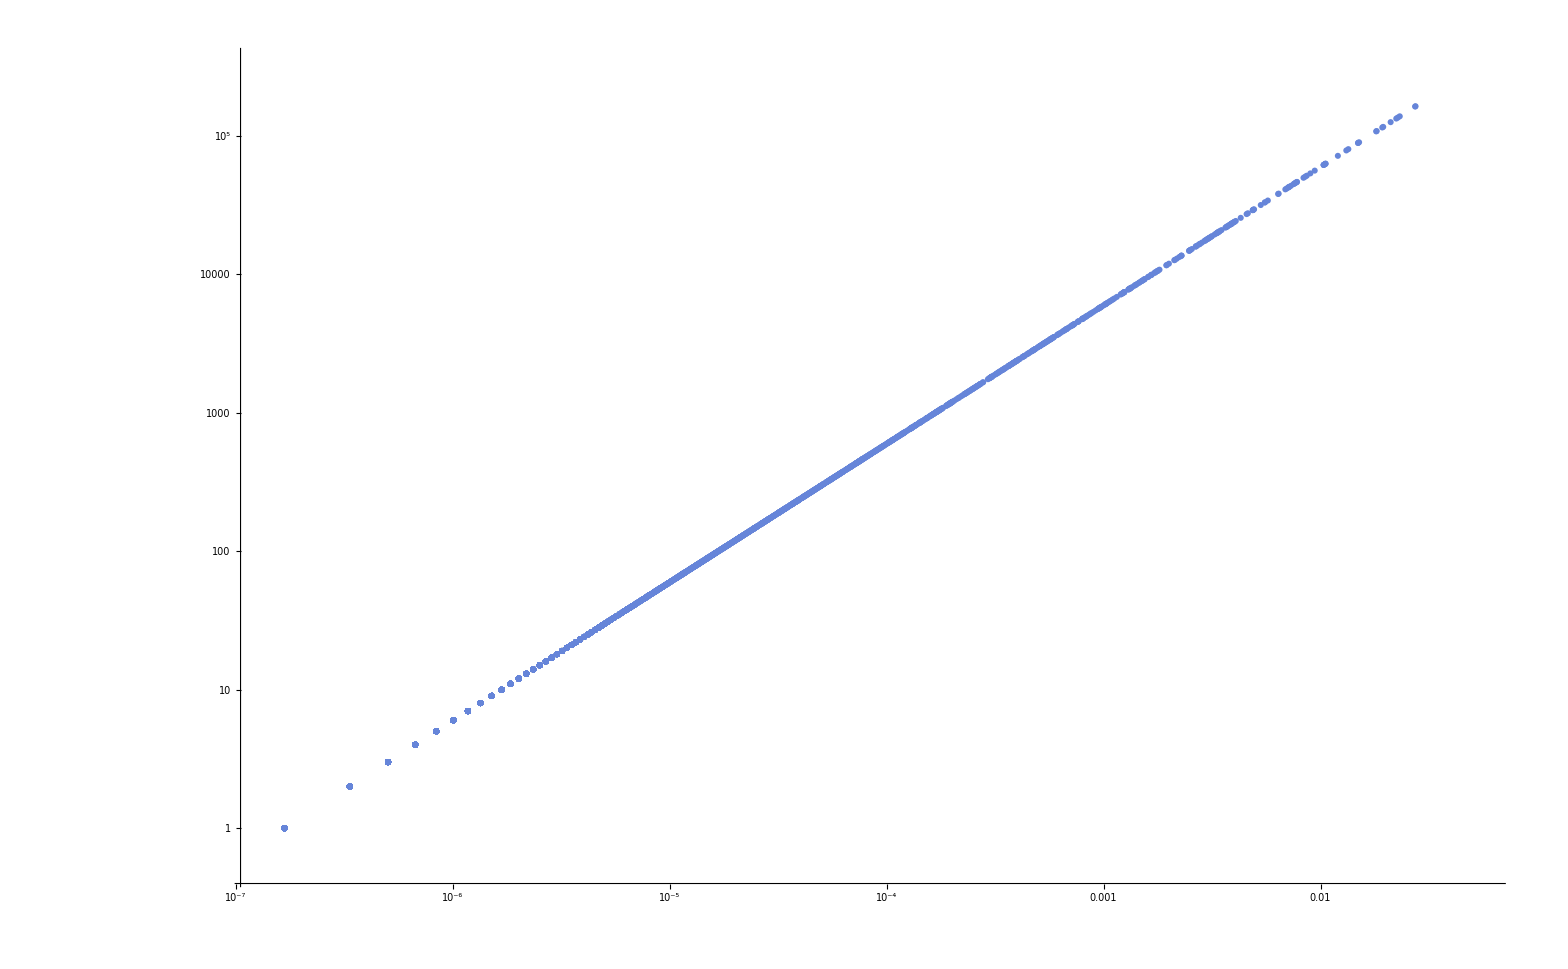

```mathematica
ListLogLogPlot[facc]
```